```mathematica
tt=Flatten[{{{1,1<->2,{18,14,8,6,2,0}},{1,1<->3,{18,14,8,6,2,0}},{1,1<->4,{18,14,8,6,2,0}},{1,1<->5,{18,14,8,6,2,0}},{1,1<->6,{18,14,8,6,2,0}},{1,2<->6,{18,14,8,6,2,0}},{1,2<->7,{18,14,8,6,2,0}},{1,2<->8,{18,14,8,6,2,0}},{1,2<->3,{18,14,8,6,2,0}},{1,3<->8,{18,14,8,6,2,0}},{1,3<->9,{18,14,8,6,2,0}},{1,3<->4,{18,14,8,6,2,0}},{1,4<->9,{18,14,8,6,2,0}},{1,4<->10,{18,14,8,6,2,0}},{1,4<->5,{18,14,8,6,2,0}},{1,5<->10,{18,14,8,6,2,0}},{1,5<->11,{18,14,8,6,2,0}},{1,5<->6,{18,14,8,6,2,0}},{1,6<->11,{18,14,8,6,2,0}},{1,6<->7,{18,14,8,6,2,0}},{1,7<->11,{18,14,8,6,2,0}},{1,7<->12,{18,14,8,6,2,0}},{1,7<->8,{18,14,8,6,2,0}},{1,8<->12,{18,14,8,6,2,0}},{1,8<->9,{18,14,8,6,2,0}},{1,9<->12,{18,14,8,6,2,0}},{1,9<->10,{18,14,8,6,2,0}},{1,10<->12,{18,14,8,6,2,0}},{1,10<->11,{18,14,8,6,2,0}},{1,11<->12,{18,14,8,6,2,0}}},{{2,1<->2,{34,32,14,18,6,0}},{2,1<->3,{34,32,14,18,6,0}},{2,1<->4,{34,32,14,18,6,0}},{2,1<->5,{34,32,14,18,6,0}},{2,1<->6,{34,32,14,18,6,0}},{2,1<->7,{34,32,14,18,6,0}},{2,2<->7,{34,27,14,13,4,0}},{2,2<->8,{39,27,19,8,3,0}},{2,2<->9,{39,27,19,8,3,0}},{2,2<->3,{34,27,14,13,4,0}},{2,3<->9,{39,27,19,8,3,0}},{2,3<->10,{39,27,19,8,3,0}},{2,3<->4,{34,27,14,13,4,0}},{2,4<->10,{39,27,19,8,3,0}},{2,4<->11,{39,27,19,8,3,0}},{2,4<->5,{34,27,14,13,4,0}},{2,5<->11,{39,27,19,8,3,0}},{2,5<->12,{39,27,19,8,3,0}},{2,5<->6,{34,27,14,13,4,0}},{2,6<->12,{39,27,19,8,3,0}},{2,6<->13,{39,27,19,8,3,0}},{2,6<->7,{34,27,14,13,4,0}},{2,7<->13,{39,27,19,8,3,0}},{2,7<->8,{39,27,19,8,3,0}},{2,8<->13,{34,27,14,13,4,0}},{2,8<->14,{34,32,14,18,6,0}},{2,8<->9,{34,27,14,13,4,0}},{2,9<->14,{34,32,14,18,6,0}},{2,9<->10,{34,27,14,13,4,0}},{2,10<->14,{34,32,14,18,6,0}},{2,10<->11,{34,27,14,13,4,0}},{2,11<->14,{34,32,14,18,6,0}},{2,11<->12,{34,27,14,13,4,0}},{2,12<->14,{34,32,14,18,6,0}},{2,12<->13,{34,27,14,13,4,0}},{2,13<->14,{34,32,14,18,6,0}}},{{3,1<->2,{46,28,14,14,2,0}},{3,1<->3,{44,32,12,20,4,0}},{3,1<->4,{46,28,14,14,2,0}},{3,1<->5,{46,28,14,14,2,0}},{3,1<->6,{44,32,12,20,4,0}},{3,1<->7,{46,28,14,14,2,0}},{3,2<->7,{52,36,20,16,4,0}},{3,2<->8,{46,28,14,14,2,0}},{3,2<->9,{48,34,16,18,4,0}},{3,2<->3,{48,34,16,18,4,0}},{3,3<->9,{50,30,18,12,2,0}},{3,3<->10,{50,30,18,12,2,0}},{3,3<->4,{48,34,16,18,4,0}},{3,4<->10,{48,34,16,18,4,0}},{3,4<->11,{46,28,14,14,2,0}},{3,4<->5,{52,36,20,16,4,0}},{3,5<->11,{46,28,14,14,2,0}},{3,5<->12,{48,34,16,18,4,0}},{3,5<->6,{48,34,16,18,4,0}},{3,6<->12,{50,30,18,12,2,0}},{3,6<->13,{50,30,18,12,2,0}},{3,6<->7,{48,34,16,18,4,0}},{3,7<->13,{48,34,16,18,4,0}},{3,7<->8,{46,28,14,14,2,0}},{3,8<->13,{44,32,12,20,4,0}},{3,8<->14,{46,28,14,14,2,0}},{3,8<->15,{46,28,14,14,2,0}},{3,8<->9,{44,32,12,20,4,0}},{3,9<->15,{48,34,16,18,4,0}},{3,9<->10,{50,30,18,12,2,0}},{3,10<->15,{48,34,16,18,4,0}},{3,10<->11,{44,32,12,20,4,0}},{3,11<->15,{46,28,14,14,2,0}},{3,11<->14,{46,28,14,14,2,0}},{3,11<->12,{44,32,12,20,4,0}},{3,12<->14,{48,34,16,18,4,0}},{3,12<->13,{50,30,18,12,2,0}},{3,13<->14,{48,34,16,18,4,0}},{3,14<->15,{52,36,20,16,4,0}}},{{4,1<->2,{62,66,32,34,14,0}},{4,1<->3,{42,26,12,14,2,0}},{4,1<->4,{62,46,32,14,6,0}},{4,1<->5,{62,46,32,14,6,0}},{4,1<->6,{42,26,12,14,2,0}},{4,2<->6,{42,26,12,14,2,0}},{4,2<->7,{62,46,32,14,6,0}},{4,2<->8,{62,46,32,14,6,0}},{4,2<->3,{42,26,12,14,2,0}},{4,3<->8,{42,26,12,14,2,0}},{4,3<->9,{42,26,12,14,2,0}},{4,3<->10,{42,26,12,14,2,0}},{4,3<->4,{42,26,12,14,2,0}},{4,4<->10,{62,66,32,34,14,0}},{4,4<->11,{42,26,12,14,2,0}},{4,4<->5,{62,46,32,14,6,0}},{4,5<->11,{42,26,12,14,2,0}},{4,5<->12,{62,66,32,34,14,0}},{4,5<->6,{42,26,12,14,2,0}},{4,6<->12,{42,26,12,14,2,0}},{4,6<->13,{42,26,12,14,2,0}},{4,6<->7,{42,26,12,14,2,0}},{4,7<->13,{62,66,32,34,14,0}},{4,7<->14,{42,26,12,14,2,0}},{4,7<->8,{62,46,32,14,6,0}},{4,8<->14,{42,26,12,14,2,0}},{4,8<->9,{62,66,32,34,14,0}},{4,9<->14,{42,26,12,14,2,0}},{4,9<->15,{62,46,32,14,6,0}},{4,9<->10,{62,46,32,14,6,0}},{4,10<->15,{62,46,32,14,6,0}},{4,10<->11,{42,26,12,14,2,0}},{4,11<->15,{42,26,12,14,2,0}},{4,11<->16,{42,26,12,14,2,0}},{4,11<->12,{42,26,12,14,2,0}},{4,12<->16,{62,46,32,14,6,0}},{4,12<->13,{62,46,32,14,6,0}},{4,13<->16,{62,46,32,14,6,0}},{4,13<->14,{42,26,12,14,2,0}},{4,14<->16,{42,26,12,14,2,0}},{4,14<->15,{42,26,12,14,2,0}},{4,15<->16,{62,66,32,34,14,0}}},{{5,1<->2,{59,57,32,25,11,0}},{5,1<->3,{46,33,19,14,4,0}},{5,1<->4,{51,38,24,14,5,0}},{5,1<->5,{59,52,32,20,9,0}},{5,1<->6,{40,25,13,12,2,0}},{5,2<->6,{46,33,19,14,4,0}},{5,2<->7,{51,38,24,14,5,0}},{5,2<->8,{59,52,32,20,9,0}},{5,2<->3,{40,25,13,12,2,0}},{5,3<->8,{50,40,23,17,6,0}},{5,3<->9,{45,35,18,17,5,0}},{5,3<->10,{36,18,9,9,0,0}},{5,3<->4,{54,47,27,20,8,0}},{5,4<->10,{45,35,18,17,5,0}},{5,4<->11,{54,47,27,20,8,0}},{5,4<->5,{51,38,24,14,5,0}},{5,5<->11,{56,48,29,19,8,0}},{5,5<->12,{54,47,27,20,8,0}},{5,5<->6,{50,40,23,17,6,0}},{5,6<->12,{45,35,18,17,5,0}},{5,6<->13,{36,18,9,9,0,0}},{5,6<->7,{54,47,27,20,8,0}},{5,7<->13,{45,35,18,17,5,0}},{5,7<->14,{54,47,27,20,8,0}},{5,7<->8,{51,38,24,14,5,0}},{5,8<->14,{56,48,29,19,8,0}},{5,8<->9,{54,47,27,20,8,0}},{5,9<->14,{51,38,24,14,5,0}},{5,9<->15,{51,38,24,14,5,0}},{5,9<->10,{54,47,27,20,8,0}},{5,10<->15,{46,33,19,14,4,0}},{5,10<->16,{40,25,13,12,2,0}},{5,10<->11,{50,40,23,17,6,0}},{5,11<->16,{59,52,32,20,9,0}},{5,11<->12,{51,38,24,14,5,0}},{5,12<->16,{51,38,24,14,5,0}},{5,12<->13,{54,47,27,20,8,0}},{5,13<->16,{46,33,19,14,4,0}},{5,13<->15,{40,25,13,12,2,0}},{5,13<->14,{50,40,23,17,6,0}},{5,14<->15,{59,52,32,20,9,0}},{5,15<->16,{59,57,32,25,11,0}}},{{6,1<->2,{60,40,18,22,4,0}},{6,1<->3,{69,52,27,25,7,0}},{6,1<->4,{66,43,24,19,4,0}},{6,1<->5,{66,43,24,19,4,0}},{6,1<->6,{69,52,27,25,7,0}},{6,2<->6,{60,40,18,22,4,0}},{6,2<->7,{60,40,18,22,4,0}},{6,2<->8,{60,40,18,22,4,0}},{6,2<->9,{60,40,18,22,4,0}},{6,2<->10,{60,40,18,22,4,0}},{6,2<->3,{60,40,18,22,4,0}},{6,3<->10,{69,52,27,25,7,0}},{6,3<->11,{66,43,24,19,4,0}},{6,3<->4,{66,43,24,19,4,0}},{6,4<->11,{69,52,27,25,7,0}},{6,4<->12,{60,40,18,22,4,0}},{6,4<->5,{69,52,27,25,7,0}},{6,5<->12,{60,40,18,22,4,0}},{6,5<->13,{69,52,27,25,7,0}},{6,5<->6,{66,43,24,19,4,0}},{6,6<->13,{66,43,24,19,4,0}},{6,6<->7,{69,52,27,25,7,0}},{6,7<->13,{66,43,24,19,4,0}},{6,7<->14,{66,43,24,19,4,0}},{6,7<->8,{69,52,27,25,7,0}},{6,8<->14,{66,43,24,19,4,0}},{6,8<->15,{66,43,24,19,4,0}},{6,8<->9,{69,52,27,25,7,0}},{6,9<->15,{66,43,24,19,4,0}},{6,9<->16,{66,43,24,19,4,0}},{6,9<->10,{69,52,27,25,7,0}},{6,10<->16,{66,43,24,19,4,0}},{6,10<->11,{66,43,24,19,4,0}},{6,11<->16,{69,52,27,25,7,0}},{6,11<->12,{60,40,18,22,4,0}},{6,12<->16,{60,40,18,22,4,0}},{6,12<->15,{60,40,18,22,4,0}},{6,12<->14,{60,40,18,22,4,0}},{6,12<->13,{60,40,18,22,4,0}},{6,13<->14,{69,52,27,25,7,0}},{6,14<->15,{69,52,27,25,7,0}},{6,15<->16,{69,52,27,25,7,0}}},{{7,1<->2,{48,44,32,12,8,0}},{7,1<->3,{44,42,28,14,8,0}},{7,1<->4,{44,47,28,19,10,0}},{7,1<->5,{43,44,27,17,9,0}},{7,1<->6,{46,43,30,13,8,0}},{7,2<->6,{46,43,30,13,8,0}},{7,2<->7,{43,44,27,17,9,0}},{7,2<->8,{44,47,28,19,10,0}},{7,2<->3,{44,42,28,14,8,0}},{7,3<->8,{38,34,22,12,6,0}},{7,3<->9,{46,48,30,18,10,0}},{7,3<->4,{38,34,22,12,6,0}},{7,4<->9,{38,34,22,12,6,0}},{7,4<->10,{50,50,34,16,10,0}},{7,4<->11,{37,36,21,15,7,0}},{7,4<->5,{44,37,28,9,6,0}},{7,5<->11,{44,37,28,9,6,0}},{7,5<->12,{43,44,27,17,9,0}},{7,5<->6,{36,38,20,18,8,0}},{7,6<->12,{46,43,30,13,8,0}},{7,6<->13,{46,43,30,13,8,0}},{7,6<->7,{36,38,20,18,8,0}},{7,7<->13,{43,44,27,17,9,0}},{7,7<->14,{44,37,28,9,6,0}},{7,7<->8,{44,37,28,9,6,0}},{7,8<->14,{37,36,21,15,7,0}},{7,8<->15,{50,50,34,16,10,0}},{7,8<->9,{38,34,22,12,6,0}},{7,9<->15,{44,42,28,14,8,0}},{7,9<->10,{44,42,28,14,8,0}},{7,10<->15,{52,56,36,20,12,0}},{7,10<->16,{44,42,28,14,8,0}},{7,10<->11,{50,50,34,16,10,0}},{7,11<->16,{38,34,22,12,6,0}},{7,11<->17,{38,34,22,12,6,0}},{7,11<->12,{44,47,28,19,10,0}},{7,12<->17,{44,42,28,14,8,0}},{7,12<->13,{48,44,32,12,8,0}},{7,13<->17,{44,42,28,14,8,0}},{7,13<->14,{44,47,28,19,10,0}},{7,14<->17,{38,34,22,12,6,0}},{7,14<->16,{38,34,22,12,6,0}},{7,14<->15,{50,50,34,16,10,0}},{7,15<->16,{44,42,28,14,8,0}},{7,16<->17,{46,48,30,18,10,0}}},{{8,1<->2,{55,45,33,12,7,0}},{8,1<->3,{56,53,34,19,10,0}},{8,1<->4,{50,50,28,22,10,0}},{8,1<->5,{52,51,30,21,10,0}},{8,1<->6,{57,51,35,16,9,0}},{8,2<->6,{50,45,28,17,8,0}},{8,2<->7,{48,49,26,23,10,0}},{8,2<->8,{49,47,27,20,9,0}},{8,2<->3,{53,44,31,13,7,0}},{8,3<->8,{45,50,23,27,11,0}},{8,3<->9,{53,44,31,13,7,0}},{8,3<->10,{56,53,34,19,10,0}},{8,3<->4,{37,36,15,21,7,0}},{8,4<->10,{50,50,28,22,10,0}},{8,4<->11,{50,50,28,22,10,0}},{8,4<->12,{37,36,15,21,7,0}},{8,4<->5,{50,50,28,22,10,0}},{8,5<->12,{56,53,34,19,10,0}},{8,5<->13,{55,45,33,12,7,0}},{8,5<->6,{57,51,35,16,9,0}},{8,6<->13,{50,45,28,17,8,0}},{8,6<->7,{56,58,34,24,12,0}},{8,7<->13,{48,49,26,23,10,0}},{8,7<->14,{56,43,34,9,6,0}},{8,7<->15,{78,94,56,38,22,0}},{8,7<->8,{56,43,34,9,6,0}},{8,8<->15,{56,43,34,9,6,0}},{8,8<->9,{49,47,27,20,9,0}},{8,9<->15,{48,49,26,23,10,0}},{8,9<->16,{50,45,28,17,8,0}},{8,9<->10,{55,45,33,12,7,0}},{8,10<->16,{57,51,35,16,9,0}},{8,10<->11,{52,51,30,21,10,0}},{8,11<->16,{57,51,35,16,9,0}},{8,11<->17,{55,45,33,12,7,0}},{8,11<->12,{56,53,34,19,10,0}},{8,12<->17,{53,44,31,13,7,0}},{8,12<->14,{45,50,23,27,11,0}},{8,12<->13,{53,44,31,13,7,0}},{8,13<->14,{49,47,27,20,9,0}},{8,14<->17,{49,47,27,20,9,0}},{8,14<->15,{56,43,34,9,6,0}},{8,15<->17,{48,49,26,23,10,0}},{8,15<->16,{56,58,34,24,12,0}},{8,16<->17,{50,45,28,17,8,0}}},{{9,1<->2,{58,44,26,18,6,0}},{9,1<->3,{81,78,49,29,15,0}},{9,1<->4,{58,49,26,23,8,0}},{9,1<->5,{66,53,34,19,8,0}},{9,1<->6,{68,64,36,28,12,0}},{9,1<->7,{56,48,24,24,8,0}},{9,2<->7,{74,72,42,30,14,0}},{9,2<->8,{58,44,26,18,6,0}},{9,2<->9,{70,60,38,22,10,0}},{9,2<->3,{70,60,38,22,10,0}},{9,3<->9,{67,56,35,21,9,0}},{9,3<->10,{82,81,50,31,16,0}},{9,3<->4,{60,45,28,17,6,0}},{9,4<->10,{65,50,33,17,7,0}},{9,4<->11,{58,44,26,18,6,0}},{9,4<->5,{59,52,27,25,9,0}},{9,5<->11,{60,55,28,27,10,0}},{9,5<->12,{64,52,32,20,8,0}},{9,5<->6,{66,48,34,14,6,0}},{9,6<->12,{72,56,40,16,8,0}},{9,6<->13,{66,58,34,24,10,0}},{9,6<->7,{58,54,26,28,10,0}},{9,7<->13,{62,56,30,26,10,0}},{9,7<->14,{58,54,26,28,10,0}},{9,7<->8,{56,48,24,24,8,0}},{9,8<->14,{68,64,36,28,12,0}},{9,8<->15,{66,53,34,19,8,0}},{9,8<->16,{58,49,26,23,8,0}},{9,8<->9,{81,78,49,29,15,0}},{9,9<->16,{60,45,28,17,6,0}},{9,9<->10,{82,81,50,31,16,0}},{9,10<->16,{65,50,33,17,7,0}},{9,10<->11,{96,98,64,34,20,0}},{9,11<->16,{58,44,26,18,6,0}},{9,11<->15,{60,55,28,27,10,0}},{9,11<->17,{64,62,32,30,12,0}},{9,11<->12,{64,62,32,30,12,0}},{9,12<->17,{62,56,30,26,10,0}},{9,12<->13,{68,54,36,18,8,0}},{9,13<->17,{68,54,36,18,8,0}},{9,13<->14,{66,58,34,24,10,0}},{9,14<->17,{72,56,40,16,8,0}},{9,14<->15,{66,48,34,14,6,0}},{9,15<->17,{64,52,32,20,8,0}},{9,15<->16,{59,52,27,25,9,0}}},{{10,1<->2,{74,62,34,28,10,0}},{10,1<->3,{64,42,24,18,4,0}},{10,1<->4,{84,72,44,28,12,0}},{10,1<->5,{64,42,24,18,4,0}},{10,1<->6,{74,62,34,28,10,0}},{10,2<->6,{78,94,38,56,22,0}},{10,2<->7,{74,62,34,28,10,0}},{10,2<->8,{74,62,34,28,10,0}},{10,2<->9,{78,94,38,56,22,0}},{10,2<->3,{74,62,34,28,10,0}},{10,3<->9,{74,62,34,28,10,0}},{10,3<->10,{64,42,24,18,4,0}},{10,3<->4,{84,72,44,28,12,0}},{10,4<->10,{84,72,44,28,12,0}},{10,4<->11,{84,72,44,28,12,0}},{10,4<->5,{84,72,44,28,12,0}},{10,5<->11,{64,42,24,18,4,0}},{10,5<->12,{74,62,34,28,10,0}},{10,5<->6,{74,62,34,28,10,0}},{10,6<->12,{78,94,38,56,22,0}},{10,6<->13,{74,62,34,28,10,0}},{10,6<->7,{74,62,34,28,10,0}},{10,7<->13,{64,42,24,18,4,0}},{10,7<->14,{84,72,44,28,12,0}},{10,7<->8,{64,42,24,18,4,0}},{10,8<->14,{84,72,44,28,12,0}},{10,8<->15,{64,42,24,18,4,0}},{10,8<->9,{74,62,34,28,10,0}},{10,9<->15,{74,62,34,28,10,0}},{10,9<->16,{78,94,38,56,22,0}},{10,9<->10,{74,62,34,28,10,0}},{10,10<->16,{74,62,34,28,10,0}},{10,10<->11,{64,42,24,18,4,0}},{10,11<->16,{74,62,34,28,10,0}},{10,11<->12,{74,62,34,28,10,0}},{10,12<->16,{78,94,38,56,22,0}},{10,12<->17,{74,62,34,28,10,0}},{10,12<->13,{74,62,34,28,10,0}},{10,13<->17,{64,42,24,18,4,0}},{10,13<->14,{84,72,44,28,12,0}},{10,14<->17,{84,72,44,28,12,0}},{10,14<->15,{84,72,44,28,12,0}},{10,15<->17,{64,42,24,18,4,0}},{10,15<->16,{74,62,34,28,10,0}},{10,16<->17,{74,62,34,28,10,0}}},{{11,1<->2,{77,46,33,13,3,0}},{11,1<->3,{134,122,90,32,22,0}},{11,1<->4,{77,46,33,13,3,0}},{11,1<->5,{96,103,52,51,22,0}},{11,1<->6,{96,103,52,51,22,0}},{11,2<->6,{73,59,29,30,9,0}},{11,2<->7,{60,50,16,34,8,0}},{11,2<->8,{73,59,29,30,9,0}},{11,2<->3,{77,46,33,13,3,0}},{11,3<->8,{96,103,52,51,22,0}},{11,3<->9,{96,103,52,51,22,0}},{11,3<->4,{77,46,33,13,3,0}},{11,4<->9,{73,59,29,30,9,0}},{11,4<->10,{60,50,16,34,8,0}},{11,4<->5,{73,59,29,30,9,0}},{11,5<->10,{73,59,29,30,9,0}},{11,5<->11,{96,103,52,51,22,0}},{11,5<->12,{78,64,34,30,10,0}},{11,5<->6,{78,64,34,30,10,0}},{11,6<->12,{78,64,34,30,10,0}},{11,6<->13,{96,103,52,51,22,0}},{11,6<->7,{73,59,29,30,9,0}},{11,7<->13,{77,46,33,13,3,0}},{11,7<->14,{77,46,33,13,3,0}},{11,7<->8,{73,59,29,30,9,0}},{11,8<->14,{96,103,52,51,22,0}},{11,8<->15,{78,64,34,30,10,0}},{11,8<->9,{78,64,34,30,10,0}},{11,9<->15,{78,64,34,30,10,0}},{11,9<->16,{96,103,52,51,22,0}},{11,9<->10,{73,59,29,30,9,0}},{11,10<->16,{77,46,33,13,3,0}},{11,10<->11,{77,46,33,13,3,0}},{11,11<->16,{134,122,90,32,22,0}},{11,11<->17,{77,46,33,13,3,0}},{11,11<->12,{96,103,52,51,22,0}},{11,12<->17,{73,59,29,30,9,0}},{11,12<->18,{73,59,29,30,9,0}},{11,12<->13,{96,103,52,51,22,0}},{11,13<->18,{77,46,33,13,3,0}},{11,13<->14,{134,122,90,32,22,0}},{11,14<->18,{77,46,33,13,3,0}},{11,14<->15,{96,103,52,51,22,0}},{11,15<->18,{73,59,29,30,9,0}},{11,15<->17,{73,59,29,30,9,0}},{11,15<->16,{96,103,52,51,22,0}},{11,16<->17,{77,46,33,13,3,0}},{11,17<->18,{60,50,16,34,8,0}}},{{12,1<->2,{65,50,35,15,7,0}},{12,1<->3,{58,49,28,21,8,0}},{12,1<->4,{46,38,16,22,6,0}},{12,1<->5,{64,62,34,28,12,0}},{12,1<->6,{52,31,22,9,2,0}},{12,2<->6,{64,62,34,28,12,0}},{12,2<->7,{56,48,26,22,8,0}},{12,2<->8,{56,48,26,22,8,0}},{12,2<->9,{58,49,28,21,8,0}},{12,2<->3,{82,81,52,29,16,0}},{12,3<->9,{65,50,35,15,7,0}},{12,3<->10,{64,62,34,28,12,0}},{12,3<->11,{56,48,26,22,8,0}},{12,3<->4,{56,48,26,22,8,0}},{12,4<->11,{56,38,26,12,4,0}},{12,4<->12,{56,38,26,12,4,0}},{12,4<->5,{56,48,26,22,8,0}},{12,5<->12,{56,48,26,22,8,0}},{12,5<->13,{58,49,28,21,8,0}},{12,5<->14,{82,81,52,29,16,0}},{12,5<->6,{65,50,35,15,7,0}},{12,6<->14,{58,49,28,21,8,0}},{12,6<->7,{46,38,16,22,6,0}},{12,7<->14,{56,48,26,22,8,0}},{12,7<->15,{56,38,26,12,4,0}},{12,7<->8,{56,38,26,12,4,0}},{12,8<->15,{56,38,26,12,4,0}},{12,8<->16,{56,48,26,22,8,0}},{12,8<->9,{46,38,16,22,6,0}},{12,9<->16,{64,62,34,28,12,0}},{12,9<->10,{52,31,22,9,2,0}},{12,10<->16,{65,50,35,15,7,0}},{12,10<->17,{58,49,28,21,8,0}},{12,10<->11,{46,38,16,22,6,0}},{12,11<->17,{56,48,26,22,8,0}},{12,11<->12,{56,38,26,12,4,0}},{12,12<->17,{56,48,26,22,8,0}},{12,12<->13,{46,38,16,22,6,0}},{12,13<->17,{64,62,34,28,12,0}},{12,13<->18,{52,31,22,9,2,0}},{12,13<->14,{65,50,35,15,7,0}},{12,14<->18,{64,62,34,28,12,0}},{12,14<->15,{56,48,26,22,8,0}},{12,15<->18,{46,38,16,22,6,0}},{12,15<->16,{56,48,26,22,8,0}},{12,16<->18,{58,49,28,21,8,0}},{12,16<->17,{82,81,52,29,16,0}},{12,17<->18,{65,50,35,15,7,0}}},{{13,1<->2,{87,66,39,27,9,0}},{13,1<->3,{100,75,52,23,10,0}},{13,1<->4,{100,80,52,28,12,0}},{13,1<->5,{82,66,34,32,10,0}},{13,1<->6,{96,93,48,45,18,0}},{13,2<->6,{83,59,35,24,7,0}},{13,2<->7,{86,68,38,30,10,0}},{13,2<->8,{81,63,33,30,9,0}},{13,2<->3,{83,64,35,29,9,0}},{13,3<->8,{98,99,50,49,20,0}},{13,3<->9,{80,60,32,28,8,0}},{13,3<->4,{104,82,56,26,12,0}},{13,4<->9,{84,72,36,36,12,0}},{13,4<->10,{104,82,56,26,12,0}},{13,4<->11,{100,80,52,28,12,0}},{13,4<->5,{78,64,30,34,10,0}},{13,5<->11,{82,66,34,32,10,0}},{13,5<->12,{96,88,48,40,16,0}},{13,5<->13,{78,64,30,34,10,0}},{13,5<->14,{78,64,30,34,10,0}},{13,5<->6,{96,88,48,40,16,0}},{13,6<->14,{88,59,40,19,6,0}},{13,6<->7,{117,101,69,32,17,0}},{13,7<->14,{85,50,37,13,3,0}},{13,7<->15,{105,100,57,43,19,0}},{13,7<->8,{87,81,39,42,15,0}},{13,8<->15,{84,67,36,31,10,0}},{13,8<->16,{100,100,52,48,20,0}},{13,8<->9,{88,64,40,24,8,0}},{13,9<->16,{88,64,40,24,8,0}},{13,9<->10,{80,60,32,28,8,0}},{13,10<->16,{98,99,50,49,20,0}},{13,10<->17,{83,64,35,29,9,0}},{13,10<->11,{100,75,52,23,10,0}},{13,11<->17,{87,66,39,27,9,0}},{13,11<->12,{96,93,48,45,18,0}},{13,12<->17,{83,59,35,24,7,0}},{13,12<->18,{117,101,69,32,17,0}},{13,12<->13,{88,59,40,19,6,0}},{13,13<->18,{85,50,37,13,3,0}},{13,13<->15,{84,67,36,31,10,0}},{13,13<->14,{70,60,22,38,10,0}},{13,14<->15,{84,67,36,31,10,0}},{13,15<->18,{105,100,57,43,19,0}},{13,15<->16,{84,67,36,31,10,0}},{13,16<->18,{87,81,39,42,15,0}},{13,16<->17,{81,63,33,30,9,0}},{13,17<->18,{86,68,38,30,10,0}}},{{14,1<->2,{74,62,36,26,10,0}},{14,1<->3,{70,60,32,28,10,0}},{14,1<->4,{68,54,30,24,8,0}},{14,1<->5,{78,64,40,24,10,0}},{14,1<->6,{70,50,32,18,6,0}},{14,2<->6,{74,62,36,26,10,0}},{14,2<->7,{79,67,41,26,11,0}},{14,2<->8,{69,57,31,26,9,0}},{14,2<->9,{69,57,31,26,9,0}},{14,2<->3,{79,67,41,26,11,0}},{14,3<->9,{85,70,47,23,11,0}},{14,3<->10,{73,54,35,19,7,0}},{14,3<->4,{83,79,45,34,15,0}},{14,4<->10,{65,55,27,28,9,0}},{14,4<->11,{72,56,34,22,8,0}},{14,4<->12,{104,102,66,36,20,0}},{14,4<->5,{64,52,26,26,8,0}},{14,5<->12,{68,54,30,24,8,0}},{14,5<->13,{68,54,30,24,8,0}},{14,5<->14,{64,52,26,26,8,0}},{14,5<->6,{78,64,40,24,10,0}},{14,6<->14,{68,54,30,24,8,0}},{14,6<->7,{70,60,32,28,10,0}},{14,7<->14,{83,79,45,34,15,0}},{14,7<->15,{73,54,35,19,7,0}},{14,7<->8,{85,70,47,23,11,0}},{14,8<->15,{63,34,25,9,1,0}},{14,8<->16,{83,79,45,34,15,0}},{14,8<->9,{60,50,22,28,8,0}},{14,9<->16,{83,79,45,34,15,0}},{14,9<->10,{63,34,25,9,1,0}},{14,10<->16,{75,65,37,28,11,0}},{14,10<->11,{54,42,16,26,6,0}},{14,11<->16,{68,64,30,34,12,0}},{14,11<->17,{64,42,26,16,4,0}},{14,11<->12,{72,46,34,12,4,0}},{14,12<->17,{92,86,54,32,16,0}},{14,12<->13,{84,82,46,36,16,0}},{14,13<->17,{92,86,54,32,16,0}},{14,13<->18,{72,46,34,12,4,0}},{14,13<->14,{104,102,66,36,20,0}},{14,14<->18,{72,56,34,22,8,0}},{14,14<->15,{65,55,27,28,9,0}},{14,15<->18,{54,42,16,26,6,0}},{14,15<->16,{75,65,37,28,11,0}},{14,16<->18,{68,64,30,34,12,0}},{14,16<->17,{108,114,70,44,24,0}},{14,17<->18,{64,42,26,16,4,0}}},{{15,1<->2,{94,72,42,30,10,0}},{15,1<->3,{88,64,36,28,8,0}},{15,1<->4,{110,100,58,42,18,0}},{15,1<->5,{80,50,28,22,4,0}},{15,1<->6,{108,94,56,38,16,0}},{15,2<->6,{94,72,42,30,10,0}},{15,2<->7,{82,56,30,26,6,0}},{15,2<->8,{98,84,46,38,14,0}},{15,2<->3,{82,56,30,26,6,0}},{15,3<->8,{84,62,32,30,8,0}},{15,3<->9,{84,62,32,30,8,0}},{15,3<->4,{82,56,30,26,6,0}},{15,4<->9,{90,80,38,42,14,0}},{15,4<->10,{82,56,30,26,6,0}},{15,4<->11,{110,100,58,42,18,0}},{15,4<->12,{78,54,26,28,6,0}},{15,4<->5,{78,54,26,28,6,0}},{15,5<->12,{74,52,22,30,6,0}},{15,5<->13,{78,54,26,28,6,0}},{15,5<->6,{80,50,28,22,4,0}},{15,6<->13,{110,100,58,42,18,0}},{15,6<->7,{88,64,36,28,8,0}},{15,7<->13,{82,56,30,26,6,0}},{15,7<->14,{84,62,32,30,8,0}},{15,7<->8,{84,62,32,30,8,0}},{15,8<->14,{96,68,44,24,8,0}},{15,8<->15,{96,88,44,44,16,0}},{15,8<->9,{96,68,44,24,8,0}},{15,9<->15,{96,68,44,24,8,0}},{15,9<->10,{84,62,32,30,8,0}},{15,10<->15,{84,62,32,30,8,0}},{15,10<->16,{82,56,30,26,6,0}},{15,10<->11,{88,64,36,28,8,0}},{15,11<->16,{94,72,42,30,10,0}},{15,11<->17,{108,94,56,38,16,0}},{15,11<->12,{80,50,28,22,4,0}},{15,12<->17,{80,50,28,22,4,0}},{15,12<->13,{78,54,26,28,6,0}},{15,13<->17,{110,100,58,42,18,0}},{15,13<->18,{82,56,30,26,6,0}},{15,13<->14,{90,80,38,42,14,0}},{15,14<->18,{84,62,32,30,8,0}},{15,14<->15,{96,68,44,24,8,0}},{15,15<->18,{84,62,32,30,8,0}},{15,15<->16,{98,84,46,38,14,0}},{15,16<->18,{82,56,30,26,6,0}},{15,16<->17,{94,72,42,30,10,0}},{15,17<->18,{88,64,36,28,8,0}}},{{16,1<->2,{85,70,32,38,11,0}},{16,1<->3,{104,77,51,26,10,0}},{16,1<->4,{105,70,52,18,7,0}},{16,1<->5,{93,69,40,29,9,0}},{16,1<->6,{93,89,40,49,17,0}},{16,2<->6,{98,79,45,34,12,0}},{16,2<->7,{93,59,40,19,5,0}},{16,2<->8,{100,75,47,28,10,0}},{16,2<->3,{89,72,36,36,11,0}},{16,3<->8,{104,107,51,56,22,0}},{16,3<->9,{89,72,36,36,11,0}},{16,3<->10,{89,82,36,46,15,0}},{16,3<->11,{84,67,31,36,10,0}},{16,3<->4,{105,90,52,38,15,0}},{16,4<->11,{92,86,39,47,16,0}},{16,4<->12,{96,83,43,40,14,0}},{16,4<->5,{112,86,59,27,12,0}},{16,5<->12,{98,69,45,24,8,0}},{16,5<->13,{96,83,43,40,14,0}},{16,5<->6,{96,88,43,45,16,0}},{16,6<->13,{92,86,39,47,16,0}},{16,6<->14,{84,67,31,36,10,0}},{16,6<->7,{110,115,57,58,24,0}},{16,7<->14,{89,82,36,46,15,0}},{16,7<->15,{105,80,52,28,11,0}},{16,7<->8,{128,99,75,24,14,0}},{16,8<->15,{108,79,55,24,10,0}},{16,8<->9,{100,95,47,48,18,0}},{16,9<->15,{93,69,40,29,9,0}},{16,9<->16,{108,79,55,24,10,0}},{16,9<->10,{105,80,52,28,11,0}},{16,10<->16,{128,99,75,24,14,0}},{16,10<->17,{93,59,40,19,5,0}},{16,10<->11,{110,115,57,58,24,0}},{16,11<->17,{98,79,45,34,12,0}},{16,11<->18,{93,89,40,49,17,0}},{16,11<->12,{96,88,43,45,16,0}},{16,12<->18,{93,69,40,29,9,0}},{16,12<->13,{112,86,59,27,12,0}},{16,13<->18,{105,70,52,18,7,0}},{16,13<->14,{105,90,52,38,15,0}},{16,14<->18,{104,77,51,26,10,0}},{16,14<->17,{89,72,36,36,11,0}},{16,14<->16,{104,107,51,56,22,0}},{16,14<->15,{89,72,36,36,11,0}},{16,15<->16,{100,95,47,48,18,0}},{16,16<->17,{100,75,47,28,10,0}},{16,17<->18,{85,70,32,38,11,0}}},{{17,1<->2,{69,57,35,22,9,0}},{17,1<->3,{80,75,46,29,14,0}},{17,1<->4,{62,56,28,28,10,0}},{17,1<->5,{72,66,38,28,12,0}},{17,1<->6,{67,56,33,23,9,0}},{17,1<->7,{70,70,36,34,14,0}},{17,2<->7,{50,35,16,19,4,0}},{17,2<->8,{62,56,28,28,10,0}},{17,2<->9,{60,45,26,19,6,0}},{17,2<->3,{59,37,25,12,3,0}},{17,3<->9,{89,87,55,32,17,0}},{17,3<->10,{60,45,26,19,6,0}},{17,3<->4,{72,66,38,28,12,0}},{17,4<->10,{62,56,28,28,10,0}},{17,4<->11,{71,58,37,21,9,0}},{17,4<->12,{88,89,54,35,18,0}},{17,4<->5,{66,53,32,21,8,0}},{17,5<->12,{81,73,47,26,13,0}},{17,5<->13,{67,51,33,18,7,0}},{17,5<->6,{74,67,40,27,12,0}},{17,6<->13,{52,31,18,13,2,0}},{17,6<->14,{81,78,47,31,15,0}},{17,6<->7,{56,38,22,16,4,0}},{17,7<->14,{68,49,34,15,6,0}},{17,7<->8,{71,58,37,21,9,0}},{17,8<->14,{88,89,54,35,18,0}},{17,8<->15,{66,53,32,21,8,0}},{17,8<->16,{62,56,28,28,10,0}},{17,8<->9,{72,66,38,28,12,0}},{17,9<->16,{80,75,46,29,14,0}},{17,9<->10,{59,37,25,12,3,0}},{17,10<->16,{69,57,35,22,9,0}},{17,10<->11,{50,35,16,19,4,0}},{17,11<->16,{70,70,36,34,14,0}},{17,11<->17,{56,38,22,16,4,0}},{17,11<->12,{68,49,34,15,6,0}},{17,12<->17,{81,78,47,31,15,0}},{17,12<->18,{68,64,34,30,12,0}},{17,12<->13,{63,49,29,20,7,0}},{17,13<->18,{50,35,16,19,4,0}},{17,13<->14,{68,64,34,30,12,0}},{17,14<->18,{63,49,29,20,7,0}},{17,14<->15,{81,73,47,26,13,0}},{17,15<->18,{67,51,33,18,7,0}},{17,15<->17,{74,67,40,27,12,0}},{17,15<->16,{72,66,38,28,12,0}},{17,16<->17,{67,56,33,23,9,0}},{17,17<->18,{52,31,18,13,2,0}}},{{18,1<->2,{128,114,64,50,20,0}},{18,1<->3,{96,68,32,36,8,0}},{18,1<->4,{128,114,64,50,20,0}},{18,1<->5,{94,62,30,32,6,0}},{18,1<->6,{130,120,66,54,22,0}},{18,1<->7,{94,62,30,32,6,0}},{18,2<->7,{96,68,32,36,8,0}},{18,2<->8,{128,114,64,50,20,0}},{18,2<->9,{94,62,30,32,6,0}},{18,2<->10,{130,120,66,54,22,0}},{18,2<->3,{94,62,30,32,6,0}},{18,3<->10,{98,64,34,30,6,0}},{18,3<->11,{98,64,34,30,6,0}},{18,3<->4,{94,62,30,32,6,0}},{18,4<->11,{130,120,66,54,22,0}},{18,4<->12,{94,62,30,32,6,0}},{18,4<->13,{128,114,64,50,20,0}},{18,4<->5,{96,68,32,36,8,0}},{18,5<->13,{94,62,30,32,6,0}},{18,5<->14,{98,64,34,30,6,0}},{18,5<->6,{98,64,34,30,6,0}},{18,6<->14,{122,96,58,38,14,0}},{18,6<->15,{122,96,58,38,14,0}},{18,6<->7,{98,64,34,30,6,0}},{18,7<->15,{98,64,34,30,6,0}},{18,7<->8,{94,62,30,32,6,0}},{18,8<->15,{130,120,66,54,22,0}},{18,8<->16,{94,62,30,32,6,0}},{18,8<->17,{128,114,64,50,20,0}},{18,8<->9,{96,68,32,36,8,0}},{18,9<->17,{94,62,30,32,6,0}},{18,9<->18,{98,64,34,30,6,0}},{18,9<->10,{98,64,34,30,6,0}},{18,10<->18,{122,96,58,38,14,0}},{18,10<->11,{122,96,58,38,14,0}},{18,11<->18,{122,96,58,38,14,0}},{18,11<->12,{98,64,34,30,6,0}},{18,12<->18,{98,64,34,30,6,0}},{18,12<->17,{94,62,30,32,6,0}},{18,12<->13,{96,68,32,36,8,0}},{18,13<->17,{128,114,64,50,20,0}},{18,13<->16,{94,62,30,32,6,0}},{18,13<->14,{130,120,66,54,22,0}},{18,14<->16,{98,64,34,30,6,0}},{18,14<->15,{122,96,58,38,14,0}},{18,15<->16,{98,64,34,30,6,0}},{18,16<->17,{96,68,32,36,8,0}},{18,17<->18,{130,120,66,54,22,0}}}},1]
```

{{1,1<->2,{18,14,8,6,2,0}},{1,1<->3,{18,14,8,6,2,0}},{1,1<->4,{18,14,8,6,2,0}},{1,1<->5,{18,14,8,6,2,0}},{1,1<->6,{18,14,8,6,2,0}},{1,2<->6,{18,14,8,6,2,0}},{1,2<->7,{18,14,8,6,2,0}},{1,2<->8,{18,14,8,6,2,0}},{1,2<->3,{18,14,8,6,2,0}},{1,3<->8,{18,14,8,6,2,0}},{1,3<->9,{18,14,8,6,2,0}},{1,3<->4,{18,14,8,6,2,0}},{1,4<->9,{18,14,8,6,2,0}},{1,4<->10,{18,14,8,6,2,0}},{1,4<->5,{18,14,8,6,2,0}},{1,5<->10,{18,14,8,6,2,0}},{1,5<->11,{18,14,8,6,2,0}},{1,5<->6,{18,14,8,6,2,0}},{1,6<->11,{18,14,8,6,2,0}},{1,6<->7,{18,14,8,6,2,0}},{1,7<->11,{18,14,8,6,2,0}},{1,7<->12,{18,14,8,6,2,0}},{1,7<->8,{18,14,8,6,2,0}},{1,8<->12,{18,14,8,6,2,0}},{1,8<->9,{18,14,8,6,2,0}},{1,9<->12,{18,14,8,6,2,0}},{1,9<->10,{18,14,8,6,2,0}},{1,10<->12,{18,14,8,6,2,0}},{1,10<->11,{18,14,8,6,2,0}},{1,11<->12,{18,14,8,6,2,0}},{2,1<->2,{34,32,14,18,6,0}},{2,1<->3,{34,32,14,18,6,0}},{2,1<->4,{34,32,14,18,6,0}},{2,1<->5,{34,32,14,18,6,0}},{2,1<->6,{34,32,14,18,6,0}},{2,1<->7,{34,32,14,18,6,0}},{2,2<->7,{34,27,14,13,4,0}},{2,2<->8,{39,27,19,8,3,0}},{2,2<->9,{39,27,19,8,3,0}},{2,2<->3,{34,27,14,13,4,0}},{2,3<->9,{39,27,19,8,3,0}},{2,3<->10,{39,27,19,8,3,0}},{2,3<->4,{34,27,14,13,4,0}},{2,4<->10,{39,27,19,8,3,0}},{2,4<->11,{39,27,19,8,3,0}},{2,4<->5,{34,27,14,13,4,0}},{2,5<->11,{39,27,19,8,3,0}},{2,5<->12,{39,27,19,8,3,0}},{2,5<->6,{34,27,14,13,4,0}},{2,6<->12,{39,27,19,8,3,0}},{2,6<->13,{39,27,19,8,3,0}},{2,6<->7,{34,27,14,13,4,0}},{2,7<->13,{39,27,19,8,3,0}},{2,7<->8,{39,27,19,8,3,0}},{2,8<->13,{34,27,14,13,4,0}},{2,8<->14,{34,32,14,18,6,0}},{2,8<->9,{34,27,14,13,4,0}},{2,9<->14,{34,32,14,18,6,0}},{2,9<->10,{34,27,14,13,4,0}},{2,10<->14,{34,32,14,18,6,0}},{2,10<->11,{34,27,14,13,4,0}},{2,11<->14,{34,32,14,18,6,0}},{2,11<->12,{34,27,14,13,4,0}},{2,12<->14,{34,32,14,18,6,0}},{2,12<->13,{34,27,14,13,4,0}},{2,13<->14,{34,32,14,18,6,0}},{3,1<->2,{46,28,14,14,2,0}},{3,1<->3,{44,32,12,20,4,0}},{3,1<->4,{46,28,14,14,2,0}},{3,1<->5,{46,28,14,14,2,0}},{3,1<->6,{44,32,12,20,4,0}},{3,1<->7,{46,28,14,14,2,0}},{3,2<->7,{52,36,20,16,4,0}},{3,2<->8,{46,28,14,14,2,0}},{3,2<->9,{48,34,16,18,4,0}},{3,2<->3,{48,34,16,18,4,0}},{3,3<->9,{50,30,18,12,2,0}},{3,3<->10,{50,30,18,12,2,0}},{3,3<->4,{48,34,16,18,4,0}},{3,4<->10,{48,34,16,18,4,0}},{3,4<->11,{46,28,14,14,2,0}},{3,4<->5,{52,36,20,16,4,0}},{3,5<->11,{46,28,14,14,2,0}},{3,5<->12,{48,34,16,18,4,0}},{3,5<->6,{48,34,16,18,4,0}},{3,6<->12,{50,30,18,12,2,0}},{3,6<->13,{50,30,18,12,2,0}},{3,6<->7,{48,34,16,18,4,0}},{3,7<->13,{48,34,16,18,4,0}},{3,7<->8,{46,28,14,14,2,0}},{3,8<->13,{44,32,12,20,4,0}},{3,8<->14,{46,28,14,14,2,0}},{3,8<->15,{46,28,14,14,2,0}},{3,8<->9,{44,32,12,20,4,0}},{3,9<->15,{48,34,16,18,4,0}},{3,9<->10,{50,30,18,12,2,0}},{3,10<->15,{48,34,16,18,4,0}},{3,10<->11,{44,32,12,20,4,0}},{3,11<->15,{46,28,14,14,2,0}},{3,11<->14,{46,28,14,14,2,0}},{3,11<->12,{44,32,12,20,4,0}},{3,12<->14,{48,34,16,18,4,0}},{3,12<->13,{50,30,18,12,2,0}},{3,13<->14,{48,34,16,18,4,0}},{3,14<->15,{52,36,20,16,4,0}},{4,1<->2,{62,66,32,34,14,0}},{4,1<->3,{42,26,12,14,2,0}},{4,1<->4,{62,46,32,14,6,0}},{4,1<->5,{62,46,32,14,6,0}},{4,1<->6,{42,26,12,14,2,0}},{4,2<->6,{42,26,12,14,2,0}},{4,2<->7,{62,46,32,14,6,0}},{4,2<->8,{62,46,32,14,6,0}},{4,2<->3,{42,26,12,14,2,0}},{4,3<->8,{42,26,12,14,2,0}},{4,3<->9,{42,26,12,14,2,0}},{4,3<->10,{42,26,12,14,2,0}},{4,3<->4,{42,26,12,14,2,0}},{4,4<->10,{62,66,32,34,14,0}},{4,4<->11,{42,26,12,14,2,0}},{4,4<->5,{62,46,32,14,6,0}},{4,5<->11,{42,26,12,14,2,0}},{4,5<->12,{62,66,32,34,14,0}},{4,5<->6,{42,26,12,14,2,0}},{4,6<->12,{42,26,12,14,2,0}},{4,6<->13,{42,26,12,14,2,0}},{4,6<->7,{42,26,12,14,2,0}},{4,7<->13,{62,66,32,34,14,0}},{4,7<->14,{42,26,12,14,2,0}},{4,7<->8,{62,46,32,14,6,0}},{4,8<->14,{42,26,12,14,2,0}},{4,8<->9,{62,66,32,34,14,0}},{4,9<->14,{42,26,12,14,2,0}},{4,9<->15,{62,46,32,14,6,0}},{4,9<->10,{62,46,32,14,6,0}},{4,10<->15,{62,46,32,14,6,0}},{4,10<->11,{42,26,12,14,2,0}},{4,11<->15,{42,26,12,14,2,0}},{4,11<->16,{42,26,12,14,2,0}},{4,11<->12,{42,26,12,14,2,0}},{4,12<->16,{62,46,32,14,6,0}},{4,12<->13,{62,46,32,14,6,0}},{4,13<->16,{62,46,32,14,6,0}},{4,13<->14,{42,26,12,14,2,0}},{4,14<->16,{42,26,12,14,2,0}},{4,14<->15,{42,26,12,14,2,0}},{4,15<->16,{62,66,32,34,14,0}},{5,1<->2,{59,57,32,25,11,0}},{5,1<->3,{46,33,19,14,4,0}},{5,1<->4,{51,38,24,14,5,0}},{5,1<->5,{59,52,32,20,9,0}},{5,1<->6,{40,25,13,12,2,0}},{5,2<->6,{46,33,19,14,4,0}},{5,2<->7,{51,38,24,14,5,0}},{5,2<->8,{59,52,32,20,9,0}},{5,2<->3,{40,25,13,12,2,0}},{5,3<->8,{50,40,23,17,6,0}},{5,3<->9,{45,35,18,17,5,0}},{5,3<->10,{36,18,9,9,0,0}},{5,3<->4,{54,47,27,20,8,0}},{5,4<->10,{45,35,18,17,5,0}},{5,4<->11,{54,47,27,20,8,0}},{5,4<->5,{51,38,24,14,5,0}},{5,5<->11,{56,48,29,19,8,0}},{5,5<->12,{54,47,27,20,8,0}},{5,5<->6,{50,40,23,17,6,0}},{5,6<->12,{45,35,18,17,5,0}},{5,6<->13,{36,18,9,9,0,0}},{5,6<->7,{54,47,27,20,8,0}},{5,7<->13,{45,35,18,17,5,0}},{5,7<->14,{54,47,27,20,8,0}},{5,7<->8,{51,38,24,14,5,0}},{5,8<->14,{56,48,29,19,8,0}},{5,8<->9,{54,47,27,20,8,0}},{5,9<->14,{51,38,24,14,5,0}},{5,9<->15,{51,38,24,14,5,0}},{5,9<->10,{54,47,27,20,8,0}},{5,10<->15,{46,33,19,14,4,0}},{5,10<->16,{40,25,13,12,2,0}},{5,10<->11,{50,40,23,17,6,0}},{5,11<->16,{59,52,32,20,9,0}},{5,11<->12,{51,38,24,14,5,0}},{5,12<->16,{51,38,24,14,5,0}},{5,12<->13,{54,47,27,20,8,0}},{5,13<->16,{46,33,19,14,4,0}},{5,13<->15,{40,25,13,12,2,0}},{5,13<->14,{50,40,23,17,6,0}},{5,14<->15,{59,52,32,20,9,0}},{5,15<->16,{59,57,32,25,11,0}},{6,1<->2,{60,40,18,22,4,0}},{6,1<->3,{69,52,27,25,7,0}},{6,1<->4,{66,43,24,19,4,0}},{6,1<->5,{66,43,24,19,4,0}},{6,1<->6,{69,52,27,25,7,0}},{6,2<->6,{60,40,18,22,4,0}},{6,2<->7,{60,40,18,22,4,0}},{6,2<->8,{60,40,18,22,4,0}},{6,2<->9,{60,40,18,22,4,0}},{6,2<->10,{60,40,18,22,4,0}},{6,2<->3,{60,40,18,22,4,0}},{6,3<->10,{69,52,27,25,7,0}},{6,3<->11,{66,43,24,19,4,0}},{6,3<->4,{66,43,24,19,4,0}},{6,4<->11,{69,52,27,25,7,0}},{6,4<->12,{60,40,18,22,4,0}},{6,4<->5,{69,52,27,25,7,0}},{6,5<->12,{60,40,18,22,4,0}},{6,5<->13,{69,52,27,25,7,0}},{6,5<->6,{66,43,24,19,4,0}},{6,6<->13,{66,43,24,19,4,0}},{6,6<->7,{69,52,27,25,7,0}},{6,7<->13,{66,43,24,19,4,0}},{6,7<->14,{66,43,24,19,4,0}},{6,7<->8,{69,52,27,25,7,0}},{6,8<->14,{66,43,24,19,4,0}},{6,8<->15,{66,43,24,19,4,0}},{6,8<->9,{69,52,27,25,7,0}},{6,9<->15,{66,43,24,19,4,0}},{6,9<->16,{66,43,24,19,4,0}},{6,9<->10,{69,52,27,25,7,0}},{6,10<->16,{66,43,24,19,4,0}},{6,10<->11,{66,43,24,19,4,0}},{6,11<->16,{69,52,27,25,7,0}},{6,11<->12,{60,40,18,22,4,0}},{6,12<->16,{60,40,18,22,4,0}},{6,12<->15,{60,40,18,22,4,0}},{6,12<->14,{60,40,18,22,4,0}},{6,12<->13,{60,40,18,22,4,0}},{6,13<->14,{69,52,27,25,7,0}},{6,14<->15,{69,52,27,25,7,0}},{6,15<->16,{69,52,27,25,7,0}},{7,1<->2,{48,44,32,12,8,0}},{7,1<->3,{44,42,28,14,8,0}},{7,1<->4,{44,47,28,19,10,0}},{7,1<->5,{43,44,27,17,9,0}},{7,1<->6,{46,43,30,13,8,0}},{7,2<->6,{46,43,30,13,8,0}},{7,2<->7,{43,44,27,17,9,0}},{7,2<->8,{44,47,28,19,10,0}},{7,2<->3,{44,42,28,14,8,0}},{7,3<->8,{38,34,22,12,6,0}},{7,3<->9,{46,48,30,18,10,0}},{7,3<->4,{38,34,22,12,6,0}},{7,4<->9,{38,34,22,12,6,0}},{7,4<->10,{50,50,34,16,10,0}},{7,4<->11,{37,36,21,15,7,0}},{7,4<->5,{44,37,28,9,6,0}},{7,5<->11,{44,37,28,9,6,0}},{7,5<->12,{43,44,27,17,9,0}},{7,5<->6,{36,38,20,18,8,0}},{7,6<->12,{46,43,30,13,8,0}},{7,6<->13,{46,43,30,13,8,0}},{7,6<->7,{36,38,20,18,8,0}},{7,7<->13,{43,44,27,17,9,0}},{7,7<->14,{44,37,28,9,6,0}},{7,7<->8,{44,37,28,9,6,0}},{7,8<->14,{37,36,21,15,7,0}},{7,8<->15,{50,50,34,16,10,0}},{7,8<->9,{38,34,22,12,6,0}},{7,9<->15,{44,42,28,14,8,0}},{7,9<->10,{44,42,28,14,8,0}},{7,10<->15,{52,56,36,20,12,0}},{7,10<->16,{44,42,28,14,8,0}},{7,10<->11,{50,50,34,16,10,0}},{7,11<->16,{38,34,22,12,6,0}},{7,11<->17,{38,34,22,12,6,0}},{7,11<->12,{44,47,28,19,10,0}},{7,12<->17,{44,42,28,14,8,0}},{7,12<->13,{48,44,32,12,8,0}},{7,13<->17,{44,42,28,14,8,0}},{7,13<->14,{44,47,28,19,10,0}},{7,14<->17,{38,34,22,12,6,0}},{7,14<->16,{38,34,22,12,6,0}},{7,14<->15,{50,50,34,16,10,0}},{7,15<->16,{44,42,28,14,8,0}},{7,16<->17,{46,48,30,18,10,0}},{8,1<->2,{55,45,33,12,7,0}},{8,1<->3,{56,53,34,19,10,0}},{8,1<->4,{50,50,28,22,10,0}},{8,1<->5,{52,51,30,21,10,0}},{8,1<->6,{57,51,35,16,9,0}},{8,2<->6,{50,45,28,17,8,0}},{8,2<->7,{48,49,26,23,10,0}},{8,2<->8,{49,47,27,20,9,0}},{8,2<->3,{53,44,31,13,7,0}},{8,3<->8,{45,50,23,27,11,0}},{8,3<->9,{53,44,31,13,7,0}},{8,3<->10,{56,53,34,19,10,0}},{8,3<->4,{37,36,15,21,7,0}},{8,4<->10,{50,50,28,22,10,0}},{8,4<->11,{50,50,28,22,10,0}},{8,4<->12,{37,36,15,21,7,0}},{8,4<->5,{50,50,28,22,10,0}},{8,5<->12,{56,53,34,19,10,0}},{8,5<->13,{55,45,33,12,7,0}},{8,5<->6,{57,51,35,16,9,0}},{8,6<->13,{50,45,28,17,8,0}},{8,6<->7,{56,58,34,24,12,0}},{8,7<->13,{48,49,26,23,10,0}},{8,7<->14,{56,43,34,9,6,0}},{8,7<->15,{78,94,56,38,22,0}},{8,7<->8,{56,43,34,9,6,0}},{8,8<->15,{56,43,34,9,6,0}},{8,8<->9,{49,47,27,20,9,0}},{8,9<->15,{48,49,26,23,10,0}},{8,9<->16,{50,45,28,17,8,0}},{8,9<->10,{55,45,33,12,7,0}},{8,10<->16,{57,51,35,16,9,0}},{8,10<->11,{52,51,30,21,10,0}},{8,11<->16,{57,51,35,16,9,0}},{8,11<->17,{55,45,33,12,7,0}},{8,11<->12,{56,53,34,19,10,0}},{8,12<->17,{53,44,31,13,7,0}},{8,12<->14,{45,50,23,27,11,0}},{8,12<->13,{53,44,31,13,7,0}},{8,13<->14,{49,47,27,20,9,0}},{8,14<->17,{49,47,27,20,9,0}},{8,14<->15,{56,43,34,9,6,0}},{8,15<->17,{48,49,26,23,10,0}},{8,15<->16,{56,58,34,24,12,0}},{8,16<->17,{50,45,28,17,8,0}},{9,1<->2,{58,44,26,18,6,0}},{9,1<->3,{81,78,49,29,15,0}},{9,1<->4,{58,49,26,23,8,0}},{9,1<->5,{66,53,34,19,8,0}},{9,1<->6,{68,64,36,28,12,0}},{9,1<->7,{56,48,24,24,8,0}},{9,2<->7,{74,72,42,30,14,0}},{9,2<->8,{58,44,26,18,6,0}},{9,2<->9,{70,60,38,22,10,0}},{9,2<->3,{70,60,38,22,10,0}},{9,3<->9,{67,56,35,21,9,0}},{9,3<->10,{82,81,50,31,16,0}},{9,3<->4,{60,45,28,17,6,0}},{9,4<->10,{65,50,33,17,7,0}},{9,4<->11,{58,44,26,18,6,0}},{9,4<->5,{59,52,27,25,9,0}},{9,5<->11,{60,55,28,27,10,0}},{9,5<->12,{64,52,32,20,8,0}},{9,5<->6,{66,48,34,14,6,0}},{9,6<->12,{72,56,40,16,8,0}},{9,6<->13,{66,58,34,24,10,0}},{9,6<->7,{58,54,26,28,10,0}},{9,7<->13,{62,56,30,26,10,0}},{9,7<->14,{58,54,26,28,10,0}},{9,7<->8,{56,48,24,24,8,0}},{9,8<->14,{68,64,36,28,12,0}},{9,8<->15,{66,53,34,19,8,0}},{9,8<->16,{58,49,26,23,8,0}},{9,8<->9,{81,78,49,29,15,0}},{9,9<->16,{60,45,28,17,6,0}},{9,9<->10,{82,81,50,31,16,0}},{9,10<->16,{65,50,33,17,7,0}},{9,10<->11,{96,98,64,34,20,0}},{9,11<->16,{58,44,26,18,6,0}},{9,11<->15,{60,55,28,27,10,0}},{9,11<->17,{64,62,32,30,12,0}},{9,11<->12,{64,62,32,30,12,0}},{9,12<->17,{62,56,30,26,10,0}},{9,12<->13,{68,54,36,18,8,0}},{9,13<->17,{68,54,36,18,8,0}},{9,13<->14,{66,58,34,24,10,0}},{9,14<->17,{72,56,40,16,8,0}},{9,14<->15,{66,48,34,14,6,0}},{9,15<->17,{64,52,32,20,8,0}},{9,15<->16,{59,52,27,25,9,0}},{10,1<->2,{74,62,34,28,10,0}},{10,1<->3,{64,42,24,18,4,0}},{10,1<->4,{84,72,44,28,12,0}},{10,1<->5,{64,42,24,18,4,0}},{10,1<->6,{74,62,34,28,10,0}},{10,2<->6,{78,94,38,56,22,0}},{10,2<->7,{74,62,34,28,10,0}},{10,2<->8,{74,62,34,28,10,0}},{10,2<->9,{78,94,38,56,22,0}},{10,2<->3,{74,62,34,28,10,0}},{10,3<->9,{74,62,34,28,10,0}},{10,3<->10,{64,42,24,18,4,0}},{10,3<->4,{84,72,44,28,12,0}},{10,4<->10,{84,72,44,28,12,0}},{10,4<->11,{84,72,44,28,12,0}},{10,4<->5,{84,72,44,28,12,0}},{10,5<->11,{64,42,24,18,4,0}},{10,5<->12,{74,62,34,28,10,0}},{10,5<->6,{74,62,34,28,10,0}},{10,6<->12,{78,94,38,56,22,0}},{10,6<->13,{74,62,34,28,10,0}},{10,6<->7,{74,62,34,28,10,0}},{10,7<->13,{64,42,24,18,4,0}},{10,7<->14,{84,72,44,28,12,0}},{10,7<->8,{64,42,24,18,4,0}},{10,8<->14,{84,72,44,28,12,0}},{10,8<->15,{64,42,24,18,4,0}},{10,8<->9,{74,62,34,28,10,0}},{10,9<->15,{74,62,34,28,10,0}},{10,9<->16,{78,94,38,56,22,0}},{10,9<->10,{74,62,34,28,10,0}},{10,10<->16,{74,62,34,28,10,0}},{10,10<->11,{64,42,24,18,4,0}},{10,11<->16,{74,62,34,28,10,0}},{10,11<->12,{74,62,34,28,10,0}},{10,12<->16,{78,94,38,56,22,0}},{10,12<->17,{74,62,34,28,10,0}},{10,12<->13,{74,62,34,28,10,0}},{10,13<->17,{64,42,24,18,4,0}},{10,13<->14,{84,72,44,28,12,0}},{10,14<->17,{84,72,44,28,12,0}},{10,14<->15,{84,72,44,28,12,0}},{10,15<->17,{64,42,24,18,4,0}},{10,15<->16,{74,62,34,28,10,0}},{10,16<->17,{74,62,34,28,10,0}},{11,1<->2,{77,46,33,13,3,0}},{11,1<->3,{134,122,90,32,22,0}},{11,1<->4,{77,46,33,13,3,0}},{11,1<->5,{96,103,52,51,22,0}},{11,1<->6,{96,103,52,51,22,0}},{11,2<->6,{73,59,29,30,9,0}},{11,2<->7,{60,50,16,34,8,0}},{11,2<->8,{73,59,29,30,9,0}},{11,2<->3,{77,46,33,13,3,0}},{11,3<->8,{96,103,52,51,22,0}},{11,3<->9,{96,103,52,51,22,0}},{11,3<->4,{77,46,33,13,3,0}},{11,4<->9,{73,59,29,30,9,0}},{11,4<->10,{60,50,16,34,8,0}},{11,4<->5,{73,59,29,30,9,0}},{11,5<->10,{73,59,29,30,9,0}},{11,5<->11,{96,103,52,51,22,0}},{11,5<->12,{78,64,34,30,10,0}},{11,5<->6,{78,64,34,30,10,0}},{11,6<->12,{78,64,34,30,10,0}},{11,6<->13,{96,103,52,51,22,0}},{11,6<->7,{73,59,29,30,9,0}},{11,7<->13,{77,46,33,13,3,0}},{11,7<->14,{77,46,33,13,3,0}},{11,7<->8,{73,59,29,30,9,0}},{11,8<->14,{96,103,52,51,22,0}},{11,8<->15,{78,64,34,30,10,0}},{11,8<->9,{78,64,34,30,10,0}},{11,9<->15,{78,64,34,30,10,0}},{11,9<->16,{96,103,52,51,22,0}},{11,9<->10,{73,59,29,30,9,0}},{11,10<->16,{77,46,33,13,3,0}},{11,10<->11,{77,46,33,13,3,0}},{11,11<->16,{134,122,90,32,22,0}},{11,11<->17,{77,46,33,13,3,0}},{11,11<->12,{96,103,52,51,22,0}},{11,12<->17,{73,59,29,30,9,0}},{11,12<->18,{73,59,29,30,9,0}},{11,12<->13,{96,103,52,51,22,0}},{11,13<->18,{77,46,33,13,3,0}},{11,13<->14,{134,122,90,32,22,0}},{11,14<->18,{77,46,33,13,3,0}},{11,14<->15,{96,103,52,51,22,0}},{11,15<->18,{73,59,29,30,9,0}},{11,15<->17,{73,59,29,30,9,0}},{11,15<->16,{96,103,52,51,22,0}},{11,16<->17,{77,46,33,13,3,0}},{11,17<->18,{60,50,16,34,8,0}},{12,1<->2,{65,50,35,15,7,0}},{12,1<->3,{58,49,28,21,8,0}},{12,1<->4,{46,38,16,22,6,0}},{12,1<->5,{64,62,34,28,12,0}},{12,1<->6,{52,31,22,9,2,0}},{12,2<->6,{64,62,34,28,12,0}},{12,2<->7,{56,48,26,22,8,0}},{12,2<->8,{56,48,26,22,8,0}},{12,2<->9,{58,49,28,21,8,0}},{12,2<->3,{82,81,52,29,16,0}},{12,3<->9,{65,50,35,15,7,0}},{12,3<->10,{64,62,34,28,12,0}},{12,3<->11,{56,48,26,22,8,0}},{12,3<->4,{56,48,26,22,8,0}},{12,4<->11,{56,38,26,12,4,0}},{12,4<->12,{56,38,26,12,4,0}},{12,4<->5,{56,48,26,22,8,0}},{12,5<->12,{56,48,26,22,8,0}},{12,5<->13,{58,49,28,21,8,0}},{12,5<->14,{82,81,52,29,16,0}},{12,5<->6,{65,50,35,15,7,0}},{12,6<->14,{58,49,28,21,8,0}},{12,6<->7,{46,38,16,22,6,0}},{12,7<->14,{56,48,26,22,8,0}},{12,7<->15,{56,38,26,12,4,0}},{12,7<->8,{56,38,26,12,4,0}},{12,8<->15,{56,38,26,12,4,0}},{12,8<->16,{56,48,26,22,8,0}},{12,8<->9,{46,38,16,22,6,0}},{12,9<->16,{64,62,34,28,12,0}},{12,9<->10,{52,31,22,9,2,0}},{12,10<->16,{65,50,35,15,7,0}},{12,10<->17,{58,49,28,21,8,0}},{12,10<->11,{46,38,16,22,6,0}},{12,11<->17,{56,48,26,22,8,0}},{12,11<->12,{56,38,26,12,4,0}},{12,12<->17,{56,48,26,22,8,0}},{12,12<->13,{46,38,16,22,6,0}},{12,13<->17,{64,62,34,28,12,0}},{12,13<->18,{52,31,22,9,2,0}},{12,13<->14,{65,50,35,15,7,0}},{12,14<->18,{64,62,34,28,12,0}},{12,14<->15,{56,48,26,22,8,0}},{12,15<->18,{46,38,16,22,6,0}},{12,15<->16,{56,48,26,22,8,0}},{12,16<->18,{58,49,28,21,8,0}},{12,16<->17,{82,81,52,29,16,0}},{12,17<->18,{65,50,35,15,7,0}},{13,1<->2,{87,66,39,27,9,0}},{13,1<->3,{100,75,52,23,10,0}},{13,1<->4,{100,80,52,28,12,0}},{13,1<->5,{82,66,34,32,10,0}},{13,1<->6,{96,93,48,45,18,0}},{13,2<->6,{83,59,35,24,7,0}},{13,2<->7,{86,68,38,30,10,0}},{13,2<->8,{81,63,33,30,9,0}},{13,2<->3,{83,64,35,29,9,0}},{13,3<->8,{98,99,50,49,20,0}},{13,3<->9,{80,60,32,28,8,0}},{13,3<->4,{104,82,56,26,12,0}},{13,4<->9,{84,72,36,36,12,0}},{13,4<->10,{104,82,56,26,12,0}},{13,4<->11,{100,80,52,28,12,0}},{13,4<->5,{78,64,30,34,10,0}},{13,5<->11,{82,66,34,32,10,0}},{13,5<->12,{96,88,48,40,16,0}},{13,5<->13,{78,64,30,34,10,0}},{13,5<->14,{78,64,30,34,10,0}},{13,5<->6,{96,88,48,40,16,0}},{13,6<->14,{88,59,40,19,6,0}},{13,6<->7,{117,101,69,32,17,0}},{13,7<->14,{85,50,37,13,3,0}},{13,7<->15,{105,100,57,43,19,0}},{13,7<->8,{87,81,39,42,15,0}},{13,8<->15,{84,67,36,31,10,0}},{13,8<->16,{100,100,52,48,20,0}},{13,8<->9,{88,64,40,24,8,0}},{13,9<->16,{88,64,40,24,8,0}},{13,9<->10,{80,60,32,28,8,0}},{13,10<->16,{98,99,50,49,20,0}},{13,10<->17,{83,64,35,29,9,0}},{13,10<->11,{100,75,52,23,10,0}},{13,11<->17,{87,66,39,27,9,0}},{13,11<->12,{96,93,48,45,18,0}},{13,12<->17,{83,59,35,24,7,0}},{13,12<->18,{117,101,69,32,17,0}},{13,12<->13,{88,59,40,19,6,0}},{13,13<->18,{85,50,37,13,3,0}},{13,13<->15,{84,67,36,31,10,0}},{13,13<->14,{70,60,22,38,10,0}},{13,14<->15,{84,67,36,31,10,0}},{13,15<->18,{105,100,57,43,19,0}},{13,15<->16,{84,67,36,31,10,0}},{13,16<->18,{87,81,39,42,15,0}},{13,16<->17,{81,63,33,30,9,0}},{13,17<->18,{86,68,38,30,10,0}},{14,1<->2,{74,62,36,26,10,0}},{14,1<->3,{70,60,32,28,10,0}},{14,1<->4,{68,54,30,24,8,0}},{14,1<->5,{78,64,40,24,10,0}},{14,1<->6,{70,50,32,18,6,0}},{14,2<->6,{74,62,36,26,10,0}},{14,2<->7,{79,67,41,26,11,0}},{14,2<->8,{69,57,31,26,9,0}},{14,2<->9,{69,57,31,26,9,0}},{14,2<->3,{79,67,41,26,11,0}},{14,3<->9,{85,70,47,23,11,0}},{14,3<->10,{73,54,35,19,7,0}},{14,3<->4,{83,79,45,34,15,0}},{14,4<->10,{65,55,27,28,9,0}},{14,4<->11,{72,56,34,22,8,0}},{14,4<->12,{104,102,66,36,20,0}},{14,4<->5,{64,52,26,26,8,0}},{14,5<->12,{68,54,30,24,8,0}},{14,5<->13,{68,54,30,24,8,0}},{14,5<->14,{64,52,26,26,8,0}},{14,5<->6,{78,64,40,24,10,0}},{14,6<->14,{68,54,30,24,8,0}},{14,6<->7,{70,60,32,28,10,0}},{14,7<->14,{83,79,45,34,15,0}},{14,7<->15,{73,54,35,19,7,0}},{14,7<->8,{85,70,47,23,11,0}},{14,8<->15,{63,34,25,9,1,0}},{14,8<->16,{83,79,45,34,15,0}},{14,8<->9,{60,50,22,28,8,0}},{14,9<->16,{83,79,45,34,15,0}},{14,9<->10,{63,34,25,9,1,0}},{14,10<->16,{75,65,37,28,11,0}},{14,10<->11,{54,42,16,26,6,0}},{14,11<->16,{68,64,30,34,12,0}},{14,11<->17,{64,42,26,16,4,0}},{14,11<->12,{72,46,34,12,4,0}},{14,12<->17,{92,86,54,32,16,0}},{14,12<->13,{84,82,46,36,16,0}},{14,13<->17,{92,86,54,32,16,0}},{14,13<->18,{72,46,34,12,4,0}},{14,13<->14,{104,102,66,36,20,0}},{14,14<->18,{72,56,34,22,8,0}},{14,14<->15,{65,55,27,28,9,0}},{14,15<->18,{54,42,16,26,6,0}},{14,15<->16,{75,65,37,28,11,0}},{14,16<->18,{68,64,30,34,12,0}},{14,16<->17,{108,114,70,44,24,0}},{14,17<->18,{64,42,26,16,4,0}},{15,1<->2,{94,72,42,30,10,0}},{15,1<->3,{88,64,36,28,8,0}},{15,1<->4,{110,100,58,42,18,0}},{15,1<->5,{80,50,28,22,4,0}},{15,1<->6,{108,94,56,38,16,0}},{15,2<->6,{94,72,42,30,10,0}},{15,2<->7,{82,56,30,26,6,0}},{15,2<->8,{98,84,46,38,14,0}},{15,2<->3,{82,56,30,26,6,0}},{15,3<->8,{84,62,32,30,8,0}},{15,3<->9,{84,62,32,30,8,0}},{15,3<->4,{82,56,30,26,6,0}},{15,4<->9,{90,80,38,42,14,0}},{15,4<->10,{82,56,30,26,6,0}},{15,4<->11,{110,100,58,42,18,0}},{15,4<->12,{78,54,26,28,6,0}},{15,4<->5,{78,54,26,28,6,0}},{15,5<->12,{74,52,22,30,6,0}},{15,5<->13,{78,54,26,28,6,0}},{15,5<->6,{80,50,28,22,4,0}},{15,6<->13,{110,100,58,42,18,0}},{15,6<->7,{88,64,36,28,8,0}},{15,7<->13,{82,56,30,26,6,0}},{15,7<->14,{84,62,32,30,8,0}},{15,7<->8,{84,62,32,30,8,0}},{15,8<->14,{96,68,44,24,8,0}},{15,8<->15,{96,88,44,44,16,0}},{15,8<->9,{96,68,44,24,8,0}},{15,9<->15,{96,68,44,24,8,0}},{15,9<->10,{84,62,32,30,8,0}},{15,10<->15,{84,62,32,30,8,0}},{15,10<->16,{82,56,30,26,6,0}},{15,10<->11,{88,64,36,28,8,0}},{15,11<->16,{94,72,42,30,10,0}},{15,11<->17,{108,94,56,38,16,0}},{15,11<->12,{80,50,28,22,4,0}},{15,12<->17,{80,50,28,22,4,0}},{15,12<->13,{78,54,26,28,6,0}},{15,13<->17,{110,100,58,42,18,0}},{15,13<->18,{82,56,30,26,6,0}},{15,13<->14,{90,80,38,42,14,0}},{15,14<->18,{84,62,32,30,8,0}},{15,14<->15,{96,68,44,24,8,0}},{15,15<->18,{84,62,32,30,8,0}},{15,15<->16,{98,84,46,38,14,0}},{15,16<->18,{82,56,30,26,6,0}},{15,16<->17,{94,72,42,30,10,0}},{15,17<->18,{88,64,36,28,8,0}},{16,1<->2,{85,70,32,38,11,0}},{16,1<->3,{104,77,51,26,10,0}},{16,1<->4,{105,70,52,18,7,0}},{16,1<->5,{93,69,40,29,9,0}},{16,1<->6,{93,89,40,49,17,0}},{16,2<->6,{98,79,45,34,12,0}},{16,2<->7,{93,59,40,19,5,0}},{16,2<->8,{100,75,47,28,10,0}},{16,2<->3,{89,72,36,36,11,0}},{16,3<->8,{104,107,51,56,22,0}},{16,3<->9,{89,72,36,36,11,0}},{16,3<->10,{89,82,36,46,15,0}},{16,3<->11,{84,67,31,36,10,0}},{16,3<->4,{105,90,52,38,15,0}},{16,4<->11,{92,86,39,47,16,0}},{16,4<->12,{96,83,43,40,14,0}},{16,4<->5,{112,86,59,27,12,0}},{16,5<->12,{98,69,45,24,8,0}},{16,5<->13,{96,83,43,40,14,0}},{16,5<->6,{96,88,43,45,16,0}},{16,6<->13,{92,86,39,47,16,0}},{16,6<->14,{84,67,31,36,10,0}},{16,6<->7,{110,115,57,58,24,0}},{16,7<->14,{89,82,36,46,15,0}},{16,7<->15,{105,80,52,28,11,0}},{16,7<->8,{128,99,75,24,14,0}},{16,8<->15,{108,79,55,24,10,0}},{16,8<->9,{100,95,47,48,18,0}},{16,9<->15,{93,69,40,29,9,0}},{16,9<->16,{108,79,55,24,10,0}},{16,9<->10,{105,80,52,28,11,0}},{16,10<->16,{128,99,75,24,14,0}},{16,10<->17,{93,59,40,19,5,0}},{16,10<->11,{110,115,57,58,24,0}},{16,11<->17,{98,79,45,34,12,0}},{16,11<->18,{93,89,40,49,17,0}},{16,11<->12,{96,88,43,45,16,0}},{16,12<->18,{93,69,40,29,9,0}},{16,12<->13,{112,86,59,27,12,0}},{16,13<->18,{105,70,52,18,7,0}},{16,13<->14,{105,90,52,38,15,0}},{16,14<->18,{104,77,51,26,10,0}},{16,14<->17,{89,72,36,36,11,0}},{16,14<->16,{104,107,51,56,22,0}},{16,14<->15,{89,72,36,36,11,0}},{16,15<->16,{100,95,47,48,18,0}},{16,16<->17,{100,75,47,28,10,0}},{16,17<->18,{85,70,32,38,11,0}},{17,1<->2,{69,57,35,22,9,0}},{17,1<->3,{80,75,46,29,14,0}},{17,1<->4,{62,56,28,28,10,0}},{17,1<->5,{72,66,38,28,12,0}},{17,1<->6,{67,56,33,23,9,0}},{17,1<->7,{70,70,36,34,14,0}},{17,2<->7,{50,35,16,19,4,0}},{17,2<->8,{62,56,28,28,10,0}},{17,2<->9,{60,45,26,19,6,0}},{17,2<->3,{59,37,25,12,3,0}},{17,3<->9,{89,87,55,32,17,0}},{17,3<->10,{60,45,26,19,6,0}},{17,3<->4,{72,66,38,28,12,0}},{17,4<->10,{62,56,28,28,10,0}},{17,4<->11,{71,58,37,21,9,0}},{17,4<->12,{88,89,54,35,18,0}},{17,4<->5,{66,53,32,21,8,0}},{17,5<->12,{81,73,47,26,13,0}},{17,5<->13,{67,51,33,18,7,0}},{17,5<->6,{74,67,40,27,12,0}},{17,6<->13,{52,31,18,13,2,0}},{17,6<->14,{81,78,47,31,15,0}},{17,6<->7,{56,38,22,16,4,0}},{17,7<->14,{68,49,34,15,6,0}},{17,7<->8,{71,58,37,21,9,0}},{17,8<->14,{88,89,54,35,18,0}},{17,8<->15,{66,53,32,21,8,0}},{17,8<->16,{62,56,28,28,10,0}},{17,8<->9,{72,66,38,28,12,0}},{17,9<->16,{80,75,46,29,14,0}},{17,9<->10,{59,37,25,12,3,0}},{17,10<->16,{69,57,35,22,9,0}},{17,10<->11,{50,35,16,19,4,0}},{17,11<->16,{70,70,36,34,14,0}},{17,11<->17,{56,38,22,16,4,0}},{17,11<->12,{68,49,34,15,6,0}},{17,12<->17,{81,78,47,31,15,0}},{17,12<->18,{68,64,34,30,12,0}},{17,12<->13,{63,49,29,20,7,0}},{17,13<->18,{50,35,16,19,4,0}},{17,13<->14,{68,64,34,30,12,0}},{17,14<->18,{63,49,29,20,7,0}},{17,14<->15,{81,73,47,26,13,0}},{17,15<->18,{67,51,33,18,7,0}},{17,15<->17,{74,67,40,27,12,0}},{17,15<->16,{72,66,38,28,12,0}},{17,16<->17,{67,56,33,23,9,0}},{17,17<->18,{52,31,18,13,2,0}},{18,1<->2,{128,114,64,50,20,0}},{18,1<->3,{96,68,32,36,8,0}},{18,1<->4,{128,114,64,50,20,0}},{18,1<->5,{94,62,30,32,6,0}},{18,1<->6,{130,120,66,54,22,0}},{18,1<->7,{94,62,30,32,6,0}},{18,2<->7,{96,68,32,36,8,0}},{18,2<->8,{128,114,64,50,20,0}},{18,2<->9,{94,62,30,32,6,0}},{18,2<->10,{130,120,66,54,22,0}},{18,2<->3,{94,62,30,32,6,0}},{18,3<->10,{98,64,34,30,6,0}},{18,3<->11,{98,64,34,30,6,0}},{18,3<->4,{94,62,30,32,6,0}},{18,4<->11,{130,120,66,54,22,0}},{18,4<->12,{94,62,30,32,6,0}},{18,4<->13,{128,114,64,50,20,0}},{18,4<->5,{96,68,32,36,8,0}},{18,5<->13,{94,62,30,32,6,0}},{18,5<->14,{98,64,34,30,6,0}},{18,5<->6,{98,64,34,30,6,0}},{18,6<->14,{122,96,58,38,14,0}},{18,6<->15,{122,96,58,38,14,0}},{18,6<->7,{98,64,34,30,6,0}},{18,7<->15,{98,64,34,30,6,0}},{18,7<->8,{94,62,30,32,6,0}},{18,8<->15,{130,120,66,54,22,0}},{18,8<->16,{94,62,30,32,6,0}},{18,8<->17,{128,114,64,50,20,0}},{18,8<->9,{96,68,32,36,8,0}},{18,9<->17,{94,62,30,32,6,0}},{18,9<->18,{98,64,34,30,6,0}},{18,9<->10,{98,64,34,30,6,0}},{18,10<->18,{122,96,58,38,14,0}},{18,10<->11,{122,96,58,38,14,0}},{18,11<->18,{122,96,58,38,14,0}},{18,11<->12,{98,64,34,30,6,0}},{18,12<->18,{98,64,34,30,6,0}},{18,12<->17,{94,62,30,32,6,0}},{18,12<->13,{96,68,32,36,8,0}},{18,13<->17,{128,114,64,50,20,0}},{18,13<->16,{94,62,30,32,6,0}},{18,13<->14,{130,120,66,54,22,0}},{18,14<->16,{98,64,34,30,6,0}},{18,14<->15,{122,96,58,38,14,0}},{18,15<->16,{98,64,34,30,6,0}},{18,16<->17,{96,68,32,36,8,0}},{18,17<->18,{130,120,66,54,22,0}}}

```mathematica
Select[tt,#[[3,5]]==0&]
```

{{5,3<->10,{36,18,9,9,0,0}},{5,6<->13,{36,18,9,9,0,0}}}

```mathematica
ChromaticPolynomial[VertexContract[VertexContract[EdgeDelete[Graph[plantri[[5]]],{3<->10}],{4,9}],{3,10}],4]
```

0

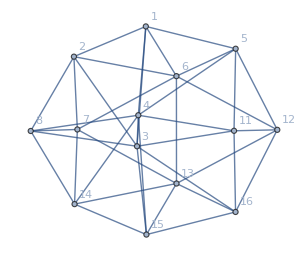

```mathematica
Graph[VertexContract[VertexContract[EdgeDelete[Graph[plantri[[5]]],{3<->10}],{4,9}],{3,10}],VertexLabels->"Name"]
```

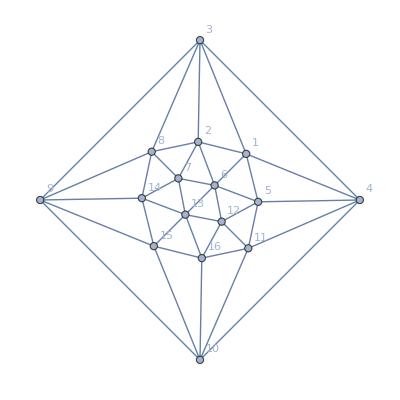

```mathematica
Graph[EdgeDelete[Graph[plantri[[5]]],{3<->10}],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

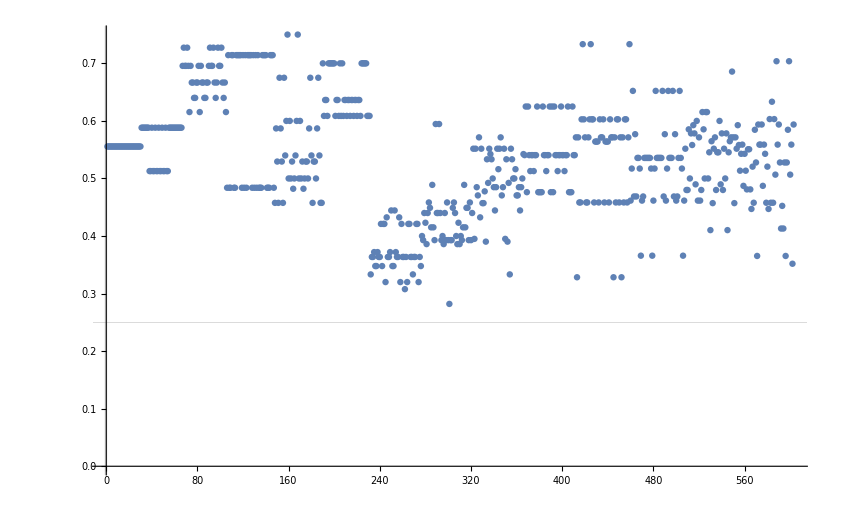

```mathematica
ListPlot[Map[With[{lambda=#[[3,1]],alfa=#[[3,3]],beta=#[[3,4]],alfa1=#[[3,5]]},
(lambda-alfa)/lambda
]&,tt],GridLines->{{-1,0,.5}, {0.25,0,0.87}}, PlotRange->All]
```

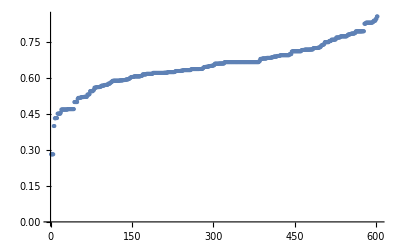

```mathematica
Map[With[{lambda=#[[3,1]],alfa=#[[3,3]],beta=#[[3,4]],alfa1=#[[3,5]]},
(lambda-beta)/lambda
]&,tt]//Sort//ListPlot
```

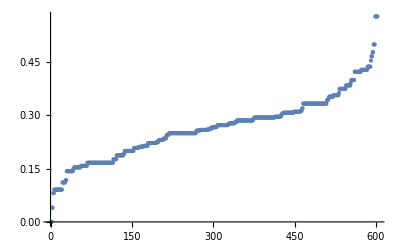

```mathematica
Map[#[[3,5]]/#[[3,3]]&,tt]//Sort//ListPlot
```

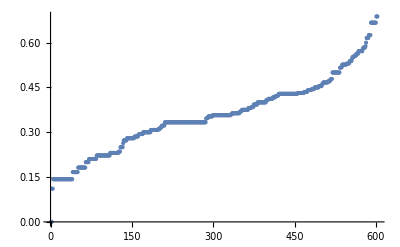

```mathematica
Map[#[[3,5]]/#[[3,4]]&,tt]//Sort//ListPlot
```

```mathematica
Select[Map[With[{lambda=#[[3,1]],alfa=#[[3,3]],beta=#[[3,4]],alfa1=#[[3,5]]},
{lambda,alfa, (lambda-alfa),beta, (lambda-beta),alfa1,(2*(alfa+beta)-lambda)==5*alfa1}
]&,tt],!#[[7]]&]
```

{}

```mathematica
TableForm[
Map[With[{lambda=#[[3,1]],alfa=#[[3,3]],beta=#[[3,4]],alfa1=#[[3,5]]},
{lambda,alfa, (lambda-alfa),beta, (lambda-beta),alfa1,(2*(alfa+beta)-lambda)==5*alfa1}
]&,tt]
]
```

18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
18 | 8 | 10 | 6 | 12 | 2 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 13 | 21 | 4 | True
39 | 19 | 20 | 8 | 31 | 3 | True
39 | 19 | 20 | 8 | 31 | 3 | True
34 | 14 | 20 | 13 | 21 | 4 | True
39 | 19 | 20 | 8 | 31 | 3 | True
39 | 19 | 20 | 8 | 31 | 3 | True
34 | 14 | 20 | 13 | 21 | 4 | True
39 | 19 | 20 | 8 | 31 | 3 | True
39 | 19 | 20 | 8 | 31 | 3 | True
34 | 14 | 20 | 13 | 21 | 4 | True
39 | 19 | 20 | 8 | 31 | 3 | True
39 | 19 | 20 | 8 | 31 | 3 | True
34 | 14 | 20 | 13 | 21 | 4 | True
39 | 19 | 20 | 8 | 31 | 3 | True
39 | 19 | 20 | 8 | 31 | 3 | True
34 | 14 | 20 | 13 | 21 | 4 | True
39 | 19 | 20 | 8 | 31 | 3 | True
39 | 19 | 20 | 8 | 31 | 3 | True
34 | 14 | 20 | 13 | 21 | 4 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 13 | 21 | 4 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 13 | 21 | 4 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 13 | 21 | 4 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 13 | 21 | 4 | True
34 | 14 | 20 | 18 | 16 | 6 | True
34 | 14 | 20 | 13 | 21 | 4 | True
34 | 14 | 20 | 18 | 16 | 6 | True
46 | 14 | 32 | 14 | 32 | 2 | True
44 | 12 | 32 | 20 | 24 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
46 | 14 | 32 | 14 | 32 | 2 | True
44 | 12 | 32 | 20 | 24 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
52 | 20 | 32 | 16 | 36 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
48 | 16 | 32 | 18 | 30 | 4 | True
48 | 16 | 32 | 18 | 30 | 4 | True
50 | 18 | 32 | 12 | 38 | 2 | True
50 | 18 | 32 | 12 | 38 | 2 | True
48 | 16 | 32 | 18 | 30 | 4 | True
48 | 16 | 32 | 18 | 30 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
52 | 20 | 32 | 16 | 36 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
48 | 16 | 32 | 18 | 30 | 4 | True
48 | 16 | 32 | 18 | 30 | 4 | True
50 | 18 | 32 | 12 | 38 | 2 | True
50 | 18 | 32 | 12 | 38 | 2 | True
48 | 16 | 32 | 18 | 30 | 4 | True
48 | 16 | 32 | 18 | 30 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
44 | 12 | 32 | 20 | 24 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
46 | 14 | 32 | 14 | 32 | 2 | True
44 | 12 | 32 | 20 | 24 | 4 | True
48 | 16 | 32 | 18 | 30 | 4 | True
50 | 18 | 32 | 12 | 38 | 2 | True
48 | 16 | 32 | 18 | 30 | 4 | True
44 | 12 | 32 | 20 | 24 | 4 | True
46 | 14 | 32 | 14 | 32 | 2 | True
46 | 14 | 32 | 14 | 32 | 2 | True
44 | 12 | 32 | 20 | 24 | 4 | True
48 | 16 | 32 | 18 | 30 | 4 | True
50 | 18 | 32 | 12 | 38 | 2 | True
48 | 16 | 32 | 18 | 30 | 4 | True
52 | 20 | 32 | 16 | 36 | 4 | True
62 | 32 | 30 | 34 | 28 | 14 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 14 | 48 | 6 | True
62 | 32 | 30 | 14 | 48 | 6 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 14 | 48 | 6 | True
62 | 32 | 30 | 14 | 48 | 6 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 34 | 28 | 14 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 14 | 48 | 6 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 34 | 28 | 14 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 34 | 28 | 14 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 14 | 48 | 6 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 34 | 28 | 14 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 14 | 48 | 6 | True
62 | 32 | 30 | 14 | 48 | 6 | True
62 | 32 | 30 | 14 | 48 | 6 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 14 | 48 | 6 | True
62 | 32 | 30 | 14 | 48 | 6 | True
62 | 32 | 30 | 14 | 48 | 6 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
42 | 12 | 30 | 14 | 28 | 2 | True
62 | 32 | 30 | 34 | 28 | 14 | True
59 | 32 | 27 | 25 | 34 | 11 | True
46 | 19 | 27 | 14 | 32 | 4 | True
51 | 24 | 27 | 14 | 37 | 5 | True
59 | 32 | 27 | 20 | 39 | 9 | True
40 | 13 | 27 | 12 | 28 | 2 | True
46 | 19 | 27 | 14 | 32 | 4 | True
51 | 24 | 27 | 14 | 37 | 5 | True
59 | 32 | 27 | 20 | 39 | 9 | True
40 | 13 | 27 | 12 | 28 | 2 | True
50 | 23 | 27 | 17 | 33 | 6 | True
45 | 18 | 27 | 17 | 28 | 5 | True
36 | 9 | 27 | 9 | 27 | 0 | True
54 | 27 | 27 | 20 | 34 | 8 | True
45 | 18 | 27 | 17 | 28 | 5 | True
54 | 27 | 27 | 20 | 34 | 8 | True
51 | 24 | 27 | 14 | 37 | 5 | True
56 | 29 | 27 | 19 | 37 | 8 | True
54 | 27 | 27 | 20 | 34 | 8 | True
50 | 23 | 27 | 17 | 33 | 6 | True
45 | 18 | 27 | 17 | 28 | 5 | True
36 | 9 | 27 | 9 | 27 | 0 | True
54 | 27 | 27 | 20 | 34 | 8 | True
45 | 18 | 27 | 17 | 28 | 5 | True
54 | 27 | 27 | 20 | 34 | 8 | True
51 | 24 | 27 | 14 | 37 | 5 | True
56 | 29 | 27 | 19 | 37 | 8 | True
54 | 27 | 27 | 20 | 34 | 8 | True
51 | 24 | 27 | 14 | 37 | 5 | True
51 | 24 | 27 | 14 | 37 | 5 | True
54 | 27 | 27 | 20 | 34 | 8 | True
46 | 19 | 27 | 14 | 32 | 4 | True
40 | 13 | 27 | 12 | 28 | 2 | True
50 | 23 | 27 | 17 | 33 | 6 | True
59 | 32 | 27 | 20 | 39 | 9 | True
51 | 24 | 27 | 14 | 37 | 5 | True
51 | 24 | 27 | 14 | 37 | 5 | True
54 | 27 | 27 | 20 | 34 | 8 | True
46 | 19 | 27 | 14 | 32 | 4 | True
40 | 13 | 27 | 12 | 28 | 2 | True
50 | 23 | 27 | 17 | 33 | 6 | True
59 | 32 | 27 | 20 | 39 | 9 | True
59 | 32 | 27 | 25 | 34 | 11 | True
60 | 18 | 42 | 22 | 38 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
66 | 24 | 42 | 19 | 47 | 4 | True
66 | 24 | 42 | 19 | 47 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
66 | 24 | 42 | 19 | 47 | 4 | True
66 | 24 | 42 | 19 | 47 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
60 | 18 | 42 | 22 | 38 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
60 | 18 | 42 | 22 | 38 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
66 | 24 | 42 | 19 | 47 | 4 | True
66 | 24 | 42 | 19 | 47 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
66 | 24 | 42 | 19 | 47 | 4 | True
66 | 24 | 42 | 19 | 47 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
66 | 24 | 42 | 19 | 47 | 4 | True
66 | 24 | 42 | 19 | 47 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
66 | 24 | 42 | 19 | 47 | 4 | True
66 | 24 | 42 | 19 | 47 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
66 | 24 | 42 | 19 | 47 | 4 | True
66 | 24 | 42 | 19 | 47 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
60 | 18 | 42 | 22 | 38 | 4 | True
69 | 27 | 42 | 25 | 44 | 7 | True
69 | 27 | 42 | 25 | 44 | 7 | True
69 | 27 | 42 | 25 | 44 | 7 | True
48 | 32 | 16 | 12 | 36 | 8 | True
44 | 28 | 16 | 14 | 30 | 8 | True
44 | 28 | 16 | 19 | 25 | 10 | True
43 | 27 | 16 | 17 | 26 | 9 | True
46 | 30 | 16 | 13 | 33 | 8 | True
46 | 30 | 16 | 13 | 33 | 8 | True
43 | 27 | 16 | 17 | 26 | 9 | True
44 | 28 | 16 | 19 | 25 | 10 | True
44 | 28 | 16 | 14 | 30 | 8 | True
38 | 22 | 16 | 12 | 26 | 6 | True
46 | 30 | 16 | 18 | 28 | 10 | True
38 | 22 | 16 | 12 | 26 | 6 | True
38 | 22 | 16 | 12 | 26 | 6 | True
50 | 34 | 16 | 16 | 34 | 10 | True
37 | 21 | 16 | 15 | 22 | 7 | True
44 | 28 | 16 | 9 | 35 | 6 | True
44 | 28 | 16 | 9 | 35 | 6 | True
43 | 27 | 16 | 17 | 26 | 9 | True
36 | 20 | 16 | 18 | 18 | 8 | True
46 | 30 | 16 | 13 | 33 | 8 | True
46 | 30 | 16 | 13 | 33 | 8 | True
36 | 20 | 16 | 18 | 18 | 8 | True
43 | 27 | 16 | 17 | 26 | 9 | True
44 | 28 | 16 | 9 | 35 | 6 | True
44 | 28 | 16 | 9 | 35 | 6 | True
37 | 21 | 16 | 15 | 22 | 7 | True
50 | 34 | 16 | 16 | 34 | 10 | True
38 | 22 | 16 | 12 | 26 | 6 | True
44 | 28 | 16 | 14 | 30 | 8 | True
44 | 28 | 16 | 14 | 30 | 8 | True
52 | 36 | 16 | 20 | 32 | 12 | True
44 | 28 | 16 | 14 | 30 | 8 | True
50 | 34 | 16 | 16 | 34 | 10 | True
38 | 22 | 16 | 12 | 26 | 6 | True
38 | 22 | 16 | 12 | 26 | 6 | True
44 | 28 | 16 | 19 | 25 | 10 | True
44 | 28 | 16 | 14 | 30 | 8 | True
48 | 32 | 16 | 12 | 36 | 8 | True
44 | 28 | 16 | 14 | 30 | 8 | True
44 | 28 | 16 | 19 | 25 | 10 | True
38 | 22 | 16 | 12 | 26 | 6 | True
38 | 22 | 16 | 12 | 26 | 6 | True
50 | 34 | 16 | 16 | 34 | 10 | True
44 | 28 | 16 | 14 | 30 | 8 | True
46 | 30 | 16 | 18 | 28 | 10 | True
55 | 33 | 22 | 12 | 43 | 7 | True
56 | 34 | 22 | 19 | 37 | 10 | True
50 | 28 | 22 | 22 | 28 | 10 | True
52 | 30 | 22 | 21 | 31 | 10 | True
57 | 35 | 22 | 16 | 41 | 9 | True
50 | 28 | 22 | 17 | 33 | 8 | True
48 | 26 | 22 | 23 | 25 | 10 | True
49 | 27 | 22 | 20 | 29 | 9 | True
53 | 31 | 22 | 13 | 40 | 7 | True
45 | 23 | 22 | 27 | 18 | 11 | True
53 | 31 | 22 | 13 | 40 | 7 | True
56 | 34 | 22 | 19 | 37 | 10 | True
37 | 15 | 22 | 21 | 16 | 7 | True
50 | 28 | 22 | 22 | 28 | 10 | True
50 | 28 | 22 | 22 | 28 | 10 | True
37 | 15 | 22 | 21 | 16 | 7 | True
50 | 28 | 22 | 22 | 28 | 10 | True
56 | 34 | 22 | 19 | 37 | 10 | True
55 | 33 | 22 | 12 | 43 | 7 | True
57 | 35 | 22 | 16 | 41 | 9 | True
50 | 28 | 22 | 17 | 33 | 8 | True
56 | 34 | 22 | 24 | 32 | 12 | True
48 | 26 | 22 | 23 | 25 | 10 | True
56 | 34 | 22 | 9 | 47 | 6 | True
78 | 56 | 22 | 38 | 40 | 22 | True
56 | 34 | 22 | 9 | 47 | 6 | True
56 | 34 | 22 | 9 | 47 | 6 | True
49 | 27 | 22 | 20 | 29 | 9 | True
48 | 26 | 22 | 23 | 25 | 10 | True
50 | 28 | 22 | 17 | 33 | 8 | True
55 | 33 | 22 | 12 | 43 | 7 | True
57 | 35 | 22 | 16 | 41 | 9 | True
52 | 30 | 22 | 21 | 31 | 10 | True
57 | 35 | 22 | 16 | 41 | 9 | True
55 | 33 | 22 | 12 | 43 | 7 | True
56 | 34 | 22 | 19 | 37 | 10 | True
53 | 31 | 22 | 13 | 40 | 7 | True
45 | 23 | 22 | 27 | 18 | 11 | True
53 | 31 | 22 | 13 | 40 | 7 | True
49 | 27 | 22 | 20 | 29 | 9 | True
49 | 27 | 22 | 20 | 29 | 9 | True
56 | 34 | 22 | 9 | 47 | 6 | True
48 | 26 | 22 | 23 | 25 | 10 | True
56 | 34 | 22 | 24 | 32 | 12 | True
50 | 28 | 22 | 17 | 33 | 8 | True
58 | 26 | 32 | 18 | 40 | 6 | True
81 | 49 | 32 | 29 | 52 | 15 | True
58 | 26 | 32 | 23 | 35 | 8 | True
66 | 34 | 32 | 19 | 47 | 8 | True
68 | 36 | 32 | 28 | 40 | 12 | True
56 | 24 | 32 | 24 | 32 | 8 | True
74 | 42 | 32 | 30 | 44 | 14 | True
58 | 26 | 32 | 18 | 40 | 6 | True
70 | 38 | 32 | 22 | 48 | 10 | True
70 | 38 | 32 | 22 | 48 | 10 | True
67 | 35 | 32 | 21 | 46 | 9 | True
82 | 50 | 32 | 31 | 51 | 16 | True
60 | 28 | 32 | 17 | 43 | 6 | True
65 | 33 | 32 | 17 | 48 | 7 | True
58 | 26 | 32 | 18 | 40 | 6 | True
59 | 27 | 32 | 25 | 34 | 9 | True
60 | 28 | 32 | 27 | 33 | 10 | True
64 | 32 | 32 | 20 | 44 | 8 | True
66 | 34 | 32 | 14 | 52 | 6 | True
72 | 40 | 32 | 16 | 56 | 8 | True
66 | 34 | 32 | 24 | 42 | 10 | True
58 | 26 | 32 | 28 | 30 | 10 | True
62 | 30 | 32 | 26 | 36 | 10 | True
58 | 26 | 32 | 28 | 30 | 10 | True
56 | 24 | 32 | 24 | 32 | 8 | True
68 | 36 | 32 | 28 | 40 | 12 | True
66 | 34 | 32 | 19 | 47 | 8 | True
58 | 26 | 32 | 23 | 35 | 8 | True
81 | 49 | 32 | 29 | 52 | 15 | True
60 | 28 | 32 | 17 | 43 | 6 | True
82 | 50 | 32 | 31 | 51 | 16 | True
65 | 33 | 32 | 17 | 48 | 7 | True
96 | 64 | 32 | 34 | 62 | 20 | True
58 | 26 | 32 | 18 | 40 | 6 | True
60 | 28 | 32 | 27 | 33 | 10 | True
64 | 32 | 32 | 30 | 34 | 12 | True
64 | 32 | 32 | 30 | 34 | 12 | True
62 | 30 | 32 | 26 | 36 | 10 | True
68 | 36 | 32 | 18 | 50 | 8 | True
68 | 36 | 32 | 18 | 50 | 8 | True
66 | 34 | 32 | 24 | 42 | 10 | True
72 | 40 | 32 | 16 | 56 | 8 | True
66 | 34 | 32 | 14 | 52 | 6 | True
64 | 32 | 32 | 20 | 44 | 8 | True
59 | 27 | 32 | 25 | 34 | 9 | True
74 | 34 | 40 | 28 | 46 | 10 | True
64 | 24 | 40 | 18 | 46 | 4 | True
84 | 44 | 40 | 28 | 56 | 12 | True
64 | 24 | 40 | 18 | 46 | 4 | True
74 | 34 | 40 | 28 | 46 | 10 | True
78 | 38 | 40 | 56 | 22 | 22 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
78 | 38 | 40 | 56 | 22 | 22 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
64 | 24 | 40 | 18 | 46 | 4 | True
84 | 44 | 40 | 28 | 56 | 12 | True
84 | 44 | 40 | 28 | 56 | 12 | True
84 | 44 | 40 | 28 | 56 | 12 | True
84 | 44 | 40 | 28 | 56 | 12 | True
64 | 24 | 40 | 18 | 46 | 4 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
78 | 38 | 40 | 56 | 22 | 22 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
64 | 24 | 40 | 18 | 46 | 4 | True
84 | 44 | 40 | 28 | 56 | 12 | True
64 | 24 | 40 | 18 | 46 | 4 | True
84 | 44 | 40 | 28 | 56 | 12 | True
64 | 24 | 40 | 18 | 46 | 4 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
78 | 38 | 40 | 56 | 22 | 22 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
64 | 24 | 40 | 18 | 46 | 4 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
78 | 38 | 40 | 56 | 22 | 22 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
64 | 24 | 40 | 18 | 46 | 4 | True
84 | 44 | 40 | 28 | 56 | 12 | True
84 | 44 | 40 | 28 | 56 | 12 | True
84 | 44 | 40 | 28 | 56 | 12 | True
64 | 24 | 40 | 18 | 46 | 4 | True
74 | 34 | 40 | 28 | 46 | 10 | True
74 | 34 | 40 | 28 | 46 | 10 | True
77 | 33 | 44 | 13 | 64 | 3 | True
134 | 90 | 44 | 32 | 102 | 22 | True
77 | 33 | 44 | 13 | 64 | 3 | True
96 | 52 | 44 | 51 | 45 | 22 | True
96 | 52 | 44 | 51 | 45 | 22 | True
73 | 29 | 44 | 30 | 43 | 9 | True
60 | 16 | 44 | 34 | 26 | 8 | True
73 | 29 | 44 | 30 | 43 | 9 | True
77 | 33 | 44 | 13 | 64 | 3 | True
96 | 52 | 44 | 51 | 45 | 22 | True
96 | 52 | 44 | 51 | 45 | 22 | True
77 | 33 | 44 | 13 | 64 | 3 | True
73 | 29 | 44 | 30 | 43 | 9 | True
60 | 16 | 44 | 34 | 26 | 8 | True
73 | 29 | 44 | 30 | 43 | 9 | True
73 | 29 | 44 | 30 | 43 | 9 | True
96 | 52 | 44 | 51 | 45 | 22 | True
78 | 34 | 44 | 30 | 48 | 10 | True
78 | 34 | 44 | 30 | 48 | 10 | True
78 | 34 | 44 | 30 | 48 | 10 | True
96 | 52 | 44 | 51 | 45 | 22 | True
73 | 29 | 44 | 30 | 43 | 9 | True
77 | 33 | 44 | 13 | 64 | 3 | True
77 | 33 | 44 | 13 | 64 | 3 | True
73 | 29 | 44 | 30 | 43 | 9 | True
96 | 52 | 44 | 51 | 45 | 22 | True
78 | 34 | 44 | 30 | 48 | 10 | True
78 | 34 | 44 | 30 | 48 | 10 | True
78 | 34 | 44 | 30 | 48 | 10 | True
96 | 52 | 44 | 51 | 45 | 22 | True
73 | 29 | 44 | 30 | 43 | 9 | True
77 | 33 | 44 | 13 | 64 | 3 | True
77 | 33 | 44 | 13 | 64 | 3 | True
134 | 90 | 44 | 32 | 102 | 22 | True
77 | 33 | 44 | 13 | 64 | 3 | True
96 | 52 | 44 | 51 | 45 | 22 | True
73 | 29 | 44 | 30 | 43 | 9 | True
73 | 29 | 44 | 30 | 43 | 9 | True
96 | 52 | 44 | 51 | 45 | 22 | True
77 | 33 | 44 | 13 | 64 | 3 | True
134 | 90 | 44 | 32 | 102 | 22 | True
77 | 33 | 44 | 13 | 64 | 3 | True
96 | 52 | 44 | 51 | 45 | 22 | True
73 | 29 | 44 | 30 | 43 | 9 | True
73 | 29 | 44 | 30 | 43 | 9 | True
96 | 52 | 44 | 51 | 45 | 22 | True
77 | 33 | 44 | 13 | 64 | 3 | True
60 | 16 | 44 | 34 | 26 | 8 | True
65 | 35 | 30 | 15 | 50 | 7 | True
58 | 28 | 30 | 21 | 37 | 8 | True
46 | 16 | 30 | 22 | 24 | 6 | True
64 | 34 | 30 | 28 | 36 | 12 | True
52 | 22 | 30 | 9 | 43 | 2 | True
64 | 34 | 30 | 28 | 36 | 12 | True
56 | 26 | 30 | 22 | 34 | 8 | True
56 | 26 | 30 | 22 | 34 | 8 | True
58 | 28 | 30 | 21 | 37 | 8 | True
82 | 52 | 30 | 29 | 53 | 16 | True
65 | 35 | 30 | 15 | 50 | 7 | True
64 | 34 | 30 | 28 | 36 | 12 | True
56 | 26 | 30 | 22 | 34 | 8 | True
56 | 26 | 30 | 22 | 34 | 8 | True
56 | 26 | 30 | 12 | 44 | 4 | True
56 | 26 | 30 | 12 | 44 | 4 | True
56 | 26 | 30 | 22 | 34 | 8 | True
56 | 26 | 30 | 22 | 34 | 8 | True
58 | 28 | 30 | 21 | 37 | 8 | True
82 | 52 | 30 | 29 | 53 | 16 | True
65 | 35 | 30 | 15 | 50 | 7 | True
58 | 28 | 30 | 21 | 37 | 8 | True
46 | 16 | 30 | 22 | 24 | 6 | True
56 | 26 | 30 | 22 | 34 | 8 | True
56 | 26 | 30 | 12 | 44 | 4 | True
56 | 26 | 30 | 12 | 44 | 4 | True
56 | 26 | 30 | 12 | 44 | 4 | True
56 | 26 | 30 | 22 | 34 | 8 | True
46 | 16 | 30 | 22 | 24 | 6 | True
64 | 34 | 30 | 28 | 36 | 12 | True
52 | 22 | 30 | 9 | 43 | 2 | True
65 | 35 | 30 | 15 | 50 | 7 | True
58 | 28 | 30 | 21 | 37 | 8 | True
46 | 16 | 30 | 22 | 24 | 6 | True
56 | 26 | 30 | 22 | 34 | 8 | True
56 | 26 | 30 | 12 | 44 | 4 | True
56 | 26 | 30 | 22 | 34 | 8 | True
46 | 16 | 30 | 22 | 24 | 6 | True
64 | 34 | 30 | 28 | 36 | 12 | True
52 | 22 | 30 | 9 | 43 | 2 | True
65 | 35 | 30 | 15 | 50 | 7 | True
64 | 34 | 30 | 28 | 36 | 12 | True
56 | 26 | 30 | 22 | 34 | 8 | True
46 | 16 | 30 | 22 | 24 | 6 | True
56 | 26 | 30 | 22 | 34 | 8 | True
58 | 28 | 30 | 21 | 37 | 8 | True
82 | 52 | 30 | 29 | 53 | 16 | True
65 | 35 | 30 | 15 | 50 | 7 | True
87 | 39 | 48 | 27 | 60 | 9 | True
100 | 52 | 48 | 23 | 77 | 10 | True
100 | 52 | 48 | 28 | 72 | 12 | True
82 | 34 | 48 | 32 | 50 | 10 | True
96 | 48 | 48 | 45 | 51 | 18 | True
83 | 35 | 48 | 24 | 59 | 7 | True
86 | 38 | 48 | 30 | 56 | 10 | True
81 | 33 | 48 | 30 | 51 | 9 | True
83 | 35 | 48 | 29 | 54 | 9 | True
98 | 50 | 48 | 49 | 49 | 20 | True
80 | 32 | 48 | 28 | 52 | 8 | True
104 | 56 | 48 | 26 | 78 | 12 | True
84 | 36 | 48 | 36 | 48 | 12 | True
104 | 56 | 48 | 26 | 78 | 12 | True
100 | 52 | 48 | 28 | 72 | 12 | True
78 | 30 | 48 | 34 | 44 | 10 | True
82 | 34 | 48 | 32 | 50 | 10 | True
96 | 48 | 48 | 40 | 56 | 16 | True
78 | 30 | 48 | 34 | 44 | 10 | True
78 | 30 | 48 | 34 | 44 | 10 | True
96 | 48 | 48 | 40 | 56 | 16 | True
88 | 40 | 48 | 19 | 69 | 6 | True
117 | 69 | 48 | 32 | 85 | 17 | True
85 | 37 | 48 | 13 | 72 | 3 | True
105 | 57 | 48 | 43 | 62 | 19 | True
87 | 39 | 48 | 42 | 45 | 15 | True
84 | 36 | 48 | 31 | 53 | 10 | True
100 | 52 | 48 | 48 | 52 | 20 | True
88 | 40 | 48 | 24 | 64 | 8 | True
88 | 40 | 48 | 24 | 64 | 8 | True
80 | 32 | 48 | 28 | 52 | 8 | True
98 | 50 | 48 | 49 | 49 | 20 | True
83 | 35 | 48 | 29 | 54 | 9 | True
100 | 52 | 48 | 23 | 77 | 10 | True
87 | 39 | 48 | 27 | 60 | 9 | True
96 | 48 | 48 | 45 | 51 | 18 | True
83 | 35 | 48 | 24 | 59 | 7 | True
117 | 69 | 48 | 32 | 85 | 17 | True
88 | 40 | 48 | 19 | 69 | 6 | True
85 | 37 | 48 | 13 | 72 | 3 | True
84 | 36 | 48 | 31 | 53 | 10 | True
70 | 22 | 48 | 38 | 32 | 10 | True
84 | 36 | 48 | 31 | 53 | 10 | True
105 | 57 | 48 | 43 | 62 | 19 | True
84 | 36 | 48 | 31 | 53 | 10 | True
87 | 39 | 48 | 42 | 45 | 15 | True
81 | 33 | 48 | 30 | 51 | 9 | True
86 | 38 | 48 | 30 | 56 | 10 | True
74 | 36 | 38 | 26 | 48 | 10 | True
70 | 32 | 38 | 28 | 42 | 10 | True
68 | 30 | 38 | 24 | 44 | 8 | True
78 | 40 | 38 | 24 | 54 | 10 | True
70 | 32 | 38 | 18 | 52 | 6 | True
74 | 36 | 38 | 26 | 48 | 10 | True
79 | 41 | 38 | 26 | 53 | 11 | True
69 | 31 | 38 | 26 | 43 | 9 | True
69 | 31 | 38 | 26 | 43 | 9 | True
79 | 41 | 38 | 26 | 53 | 11 | True
85 | 47 | 38 | 23 | 62 | 11 | True
73 | 35 | 38 | 19 | 54 | 7 | True
83 | 45 | 38 | 34 | 49 | 15 | True
65 | 27 | 38 | 28 | 37 | 9 | True
72 | 34 | 38 | 22 | 50 | 8 | True
104 | 66 | 38 | 36 | 68 | 20 | True
64 | 26 | 38 | 26 | 38 | 8 | True
68 | 30 | 38 | 24 | 44 | 8 | True
68 | 30 | 38 | 24 | 44 | 8 | True
64 | 26 | 38 | 26 | 38 | 8 | True
78 | 40 | 38 | 24 | 54 | 10 | True
68 | 30 | 38 | 24 | 44 | 8 | True
70 | 32 | 38 | 28 | 42 | 10 | True
83 | 45 | 38 | 34 | 49 | 15 | True
73 | 35 | 38 | 19 | 54 | 7 | True
85 | 47 | 38 | 23 | 62 | 11 | True
63 | 25 | 38 | 9 | 54 | 1 | True
83 | 45 | 38 | 34 | 49 | 15 | True
60 | 22 | 38 | 28 | 32 | 8 | True
83 | 45 | 38 | 34 | 49 | 15 | True
63 | 25 | 38 | 9 | 54 | 1 | True
75 | 37 | 38 | 28 | 47 | 11 | True
54 | 16 | 38 | 26 | 28 | 6 | True
68 | 30 | 38 | 34 | 34 | 12 | True
64 | 26 | 38 | 16 | 48 | 4 | True
72 | 34 | 38 | 12 | 60 | 4 | True
92 | 54 | 38 | 32 | 60 | 16 | True
84 | 46 | 38 | 36 | 48 | 16 | True
92 | 54 | 38 | 32 | 60 | 16 | True
72 | 34 | 38 | 12 | 60 | 4 | True
104 | 66 | 38 | 36 | 68 | 20 | True
72 | 34 | 38 | 22 | 50 | 8 | True
65 | 27 | 38 | 28 | 37 | 9 | True
54 | 16 | 38 | 26 | 28 | 6 | True
75 | 37 | 38 | 28 | 47 | 11 | True
68 | 30 | 38 | 34 | 34 | 12 | True
108 | 70 | 38 | 44 | 64 | 24 | True
64 | 26 | 38 | 16 | 48 | 4 | True
94 | 42 | 52 | 30 | 64 | 10 | True
88 | 36 | 52 | 28 | 60 | 8 | True
110 | 58 | 52 | 42 | 68 | 18 | True
80 | 28 | 52 | 22 | 58 | 4 | True
108 | 56 | 52 | 38 | 70 | 16 | True
94 | 42 | 52 | 30 | 64 | 10 | True
82 | 30 | 52 | 26 | 56 | 6 | True
98 | 46 | 52 | 38 | 60 | 14 | True
82 | 30 | 52 | 26 | 56 | 6 | True
84 | 32 | 52 | 30 | 54 | 8 | True
84 | 32 | 52 | 30 | 54 | 8 | True
82 | 30 | 52 | 26 | 56 | 6 | True
90 | 38 | 52 | 42 | 48 | 14 | True
82 | 30 | 52 | 26 | 56 | 6 | True
110 | 58 | 52 | 42 | 68 | 18 | True
78 | 26 | 52 | 28 | 50 | 6 | True
78 | 26 | 52 | 28 | 50 | 6 | True
74 | 22 | 52 | 30 | 44 | 6 | True
78 | 26 | 52 | 28 | 50 | 6 | True
80 | 28 | 52 | 22 | 58 | 4 | True
110 | 58 | 52 | 42 | 68 | 18 | True
88 | 36 | 52 | 28 | 60 | 8 | True
82 | 30 | 52 | 26 | 56 | 6 | True
84 | 32 | 52 | 30 | 54 | 8 | True
84 | 32 | 52 | 30 | 54 | 8 | True
96 | 44 | 52 | 24 | 72 | 8 | True
96 | 44 | 52 | 44 | 52 | 16 | True
96 | 44 | 52 | 24 | 72 | 8 | True
96 | 44 | 52 | 24 | 72 | 8 | True
84 | 32 | 52 | 30 | 54 | 8 | True
84 | 32 | 52 | 30 | 54 | 8 | True
82 | 30 | 52 | 26 | 56 | 6 | True
88 | 36 | 52 | 28 | 60 | 8 | True
94 | 42 | 52 | 30 | 64 | 10 | True
108 | 56 | 52 | 38 | 70 | 16 | True
80 | 28 | 52 | 22 | 58 | 4 | True
80 | 28 | 52 | 22 | 58 | 4 | True
78 | 26 | 52 | 28 | 50 | 6 | True
110 | 58 | 52 | 42 | 68 | 18 | True
82 | 30 | 52 | 26 | 56 | 6 | True
90 | 38 | 52 | 42 | 48 | 14 | True
84 | 32 | 52 | 30 | 54 | 8 | True
96 | 44 | 52 | 24 | 72 | 8 | True
84 | 32 | 52 | 30 | 54 | 8 | True
98 | 46 | 52 | 38 | 60 | 14 | True
82 | 30 | 52 | 26 | 56 | 6 | True
94 | 42 | 52 | 30 | 64 | 10 | True
88 | 36 | 52 | 28 | 60 | 8 | True
85 | 32 | 53 | 38 | 47 | 11 | True
104 | 51 | 53 | 26 | 78 | 10 | True
105 | 52 | 53 | 18 | 87 | 7 | True
93 | 40 | 53 | 29 | 64 | 9 | True
93 | 40 | 53 | 49 | 44 | 17 | True
98 | 45 | 53 | 34 | 64 | 12 | True
93 | 40 | 53 | 19 | 74 | 5 | True
100 | 47 | 53 | 28 | 72 | 10 | True
89 | 36 | 53 | 36 | 53 | 11 | True
104 | 51 | 53 | 56 | 48 | 22 | True
89 | 36 | 53 | 36 | 53 | 11 | True
89 | 36 | 53 | 46 | 43 | 15 | True
84 | 31 | 53 | 36 | 48 | 10 | True
105 | 52 | 53 | 38 | 67 | 15 | True
92 | 39 | 53 | 47 | 45 | 16 | True
96 | 43 | 53 | 40 | 56 | 14 | True
112 | 59 | 53 | 27 | 85 | 12 | True
98 | 45 | 53 | 24 | 74 | 8 | True
96 | 43 | 53 | 40 | 56 | 14 | True
96 | 43 | 53 | 45 | 51 | 16 | True
92 | 39 | 53 | 47 | 45 | 16 | True
84 | 31 | 53 | 36 | 48 | 10 | True
110 | 57 | 53 | 58 | 52 | 24 | True
89 | 36 | 53 | 46 | 43 | 15 | True
105 | 52 | 53 | 28 | 77 | 11 | True
128 | 75 | 53 | 24 | 104 | 14 | True
108 | 55 | 53 | 24 | 84 | 10 | True
100 | 47 | 53 | 48 | 52 | 18 | True
93 | 40 | 53 | 29 | 64 | 9 | True
108 | 55 | 53 | 24 | 84 | 10 | True
105 | 52 | 53 | 28 | 77 | 11 | True
128 | 75 | 53 | 24 | 104 | 14 | True
93 | 40 | 53 | 19 | 74 | 5 | True
110 | 57 | 53 | 58 | 52 | 24 | True
98 | 45 | 53 | 34 | 64 | 12 | True
93 | 40 | 53 | 49 | 44 | 17 | True
96 | 43 | 53 | 45 | 51 | 16 | True
93 | 40 | 53 | 29 | 64 | 9 | True
112 | 59 | 53 | 27 | 85 | 12 | True
105 | 52 | 53 | 18 | 87 | 7 | True
105 | 52 | 53 | 38 | 67 | 15 | True
104 | 51 | 53 | 26 | 78 | 10 | True
89 | 36 | 53 | 36 | 53 | 11 | True
104 | 51 | 53 | 56 | 48 | 22 | True
89 | 36 | 53 | 36 | 53 | 11 | True
100 | 47 | 53 | 48 | 52 | 18 | True
100 | 47 | 53 | 28 | 72 | 10 | True
85 | 32 | 53 | 38 | 47 | 11 | True
69 | 35 | 34 | 22 | 47 | 9 | True
80 | 46 | 34 | 29 | 51 | 14 | True
62 | 28 | 34 | 28 | 34 | 10 | True
72 | 38 | 34 | 28 | 44 | 12 | True
67 | 33 | 34 | 23 | 44 | 9 | True
70 | 36 | 34 | 34 | 36 | 14 | True
50 | 16 | 34 | 19 | 31 | 4 | True
62 | 28 | 34 | 28 | 34 | 10 | True
60 | 26 | 34 | 19 | 41 | 6 | True
59 | 25 | 34 | 12 | 47 | 3 | True
89 | 55 | 34 | 32 | 57 | 17 | True
60 | 26 | 34 | 19 | 41 | 6 | True
72 | 38 | 34 | 28 | 44 | 12 | True
62 | 28 | 34 | 28 | 34 | 10 | True
71 | 37 | 34 | 21 | 50 | 9 | True
88 | 54 | 34 | 35 | 53 | 18 | True
66 | 32 | 34 | 21 | 45 | 8 | True
81 | 47 | 34 | 26 | 55 | 13 | True
67 | 33 | 34 | 18 | 49 | 7 | True
74 | 40 | 34 | 27 | 47 | 12 | True
52 | 18 | 34 | 13 | 39 | 2 | True
81 | 47 | 34 | 31 | 50 | 15 | True
56 | 22 | 34 | 16 | 40 | 4 | True
68 | 34 | 34 | 15 | 53 | 6 | True
71 | 37 | 34 | 21 | 50 | 9 | True
88 | 54 | 34 | 35 | 53 | 18 | True
66 | 32 | 34 | 21 | 45 | 8 | True
62 | 28 | 34 | 28 | 34 | 10 | True
72 | 38 | 34 | 28 | 44 | 12 | True
80 | 46 | 34 | 29 | 51 | 14 | True
59 | 25 | 34 | 12 | 47 | 3 | True
69 | 35 | 34 | 22 | 47 | 9 | True
50 | 16 | 34 | 19 | 31 | 4 | True
70 | 36 | 34 | 34 | 36 | 14 | True
56 | 22 | 34 | 16 | 40 | 4 | True
68 | 34 | 34 | 15 | 53 | 6 | True
81 | 47 | 34 | 31 | 50 | 15 | True
68 | 34 | 34 | 30 | 38 | 12 | True
63 | 29 | 34 | 20 | 43 | 7 | True
50 | 16 | 34 | 19 | 31 | 4 | True
68 | 34 | 34 | 30 | 38 | 12 | True
63 | 29 | 34 | 20 | 43 | 7 | True
81 | 47 | 34 | 26 | 55 | 13 | True
67 | 33 | 34 | 18 | 49 | 7 | True
74 | 40 | 34 | 27 | 47 | 12 | True
72 | 38 | 34 | 28 | 44 | 12 | True
67 | 33 | 34 | 23 | 44 | 9 | True
52 | 18 | 34 | 13 | 39 | 2 | True
128 | 64 | 64 | 50 | 78 | 20 | True
96 | 32 | 64 | 36 | 60 | 8 | True
128 | 64 | 64 | 50 | 78 | 20 | True
94 | 30 | 64 | 32 | 62 | 6 | True
130 | 66 | 64 | 54 | 76 | 22 | True
94 | 30 | 64 | 32 | 62 | 6 | True
96 | 32 | 64 | 36 | 60 | 8 | True
128 | 64 | 64 | 50 | 78 | 20 | True
94 | 30 | 64 | 32 | 62 | 6 | True
130 | 66 | 64 | 54 | 76 | 22 | True
94 | 30 | 64 | 32 | 62 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
94 | 30 | 64 | 32 | 62 | 6 | True
130 | 66 | 64 | 54 | 76 | 22 | True
94 | 30 | 64 | 32 | 62 | 6 | True
128 | 64 | 64 | 50 | 78 | 20 | True
96 | 32 | 64 | 36 | 60 | 8 | True
94 | 30 | 64 | 32 | 62 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
122 | 58 | 64 | 38 | 84 | 14 | True
122 | 58 | 64 | 38 | 84 | 14 | True
98 | 34 | 64 | 30 | 68 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
94 | 30 | 64 | 32 | 62 | 6 | True
130 | 66 | 64 | 54 | 76 | 22 | True
94 | 30 | 64 | 32 | 62 | 6 | True
128 | 64 | 64 | 50 | 78 | 20 | True
96 | 32 | 64 | 36 | 60 | 8 | True
94 | 30 | 64 | 32 | 62 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
122 | 58 | 64 | 38 | 84 | 14 | True
122 | 58 | 64 | 38 | 84 | 14 | True
122 | 58 | 64 | 38 | 84 | 14 | True
98 | 34 | 64 | 30 | 68 | 6 | True
98 | 34 | 64 | 30 | 68 | 6 | True
94 | 30 | 64 | 32 | 62 | 6 | True
96 | 32 | 64 | 36 | 60 | 8 | True
128 | 64 | 64 | 50 | 78 | 20 | True
94 | 30 | 64 | 32 | 62 | 6 | True
130 | 66 | 64 | 54 | 76 | 22 | True
98 | 34 | 64 | 30 | 68 | 6 | True
122 | 58 | 64 | 38 | 84 | 14 | True
98 | 34 | 64 | 30 | 68 | 6 | True
96 | 32 | 64 | 36 | 60 | 8 | True
130 | 66 | 64 | 54 | 76 | 22 | True

```mathematica
Solve[(2*(alfa+beta)-lambda)==5*alfa1,lambda]
```

{{lambda→2 alfa-5 alfa1+2 beta}}